```mathematica
(*a set of observable transitions should read: { {{s(l), t(l), Subscript[r, l]}, {s(l̄), t(l̄), Subscript[r, l̄]}}, ... } *)
(*an event reads: x = {{s(l), t(l), Subscript[r, l]}, ...} for all l ∈ θ^-1 x*)

(*for aesthetic purposes, sorry*)
Needs["MaTeX`"]
SetDirectory[NotebookDirectory[]];
magentaviva = RGBColor[{190,52,85}/255];
pageantblue = RGBColor[{31,44,67}/255];
castletongreen = RGBColor[{28,88,64}/255];
sepia = RGBColor[{122,78,13}/255];
mark = #1 &@@@ Graphics`PlotMarkers[];

(*stationary distribution achieved by a generator*)
SteadyState[mat_] := Module[{pss},
	pss = Table[(-1)^j Det[ Drop[mat,{2},{j}] ], {j,Length@mat}];
	pss = pss/Total[pss]
]

(*define log(0/0) = 0*)
SmartLog[a_, b_] := If[ PossibleZeroQ[Chop[a]] ∧ PossibleZeroQ[Chop[b]], 0, Log[a/b]]

(*entropy production rate, "set" has to include ALL transitions*)
EPR[R_, set_] := Module[{ps},
	ps = SteadyState[R];
	Sum[( ps[[s[[1,1]]]]s[[1,3]] - ps[[s[[2,1]]]]s[[2,3]] ) SmartLog[s[[1,3]], s[[2,3]]], {s,set}]
]

(*traffic of a set of transitions*)
Kfun[set_, pss_] := Total[#3 pss[[#1]] &@@@ Flatten[set,1]]

(*survival matrix*)
Smatrix[R_, set_] := Module[{S},
	S = R;
	( S[[#2,#1]] -= #3 ) &@@@ Flatten[set,1];
	S
]

(*matrix Γ of an event x*)
Γmatrix[x_, pss_] := Module[{Γ},
	Γ = (Table[0, {i,Length[pss]}, {j,Length[pss]}]);
	(Γ[[#2,#1]] += #3) &@@@ x;
	Kfun[{x},pss]^-1 Γ
]

(*convenient functions for the statistics of events*)
Px[pss_,transitions_,R_][x_] := Kfun[{x},pss]/Kfun[transitions,pss];
Px2Gx1[pss_,transitions_,R_][x1_,x2_] := -Kfun[{x2},pss]Total[Γmatrix[x2,pss].Inverse[Smatrix[R,transitions]].Γmatrix[x1,pss].pss]
Px2tGx1[pss_,transitions_,R_][x1_,x2_,t_] := Kfun[{x2},pss]Total[Γmatrix[x2,pss].MatrixExp[t Smatrix[R,transitions]].Γmatrix[x1,pss].pss]


(*Fermi-Dirac and Bose-Einstein statistics*)
FD[ϵ_,β_]:=(1+Exp[β ϵ])^-1;
BE[ϵ_,β_]:=(Exp[β ϵ] - 1)^-1;
```

## example of functions usage

defining the double QD model

```mathematica
{Γ1,Γ2,Γ3,Γ4}={11,5,7,13};
{μ1,μ2,μ3,μ4}={4,3.5,1,7};
{β1,β2,β3,β4}={1,1,1,1};
{ϵu,ϵd,Δϵ}={2,1,5};
w0111r3=Γ3 (1-FD[ϵd+Δϵ-μ3,β3]);w1101r3=Γ3 FD[ϵd+Δϵ-μ3,β3];
w0111r4=Γ4 (1-FD[ϵd+Δϵ-μ4,β4]);w1101r4=Γ4 FD[ϵd+Δϵ-μ4,β4];
w0100r1=Γ1 FD[ϵu-μ1,β1];w0001r1=Γ1 (1-FD[ϵu-μ1,β1]);
w0100r2=Γ2 FD[ϵu-μ2,β2];w0001r2=Γ2 (1-FD[ϵu-μ2,β2]);
w1110r1=Γ1 FD[ϵu+Δϵ-μ1,β1];w1011r1=Γ1(1- FD[ϵu+Δϵ-μ1,β1]);
w1110r2=Γ2 FD[ϵu+Δϵ-μ2,β2];w1011r2=Γ2(1- FD[ϵu+Δϵ-μ2,β2]);
w1000r3=Γ3 FD[ϵd-μ3,β3];w0010r3=Γ3 (1-FD[ϵd-μ3,β3]);
w1000r4=Γ4 FD[ϵd-μ4,β4];w0010r4=Γ4 (1-FD[ϵd-μ4,β4]);
(*01,11,10,00*)
R=({{0, w0111r3+w0111r4, 0, w0100r1+w0100r2}, {w1101r3+w1101r4, 0, w1110r1+w1110r2, 0}, {0, w1011r1+w1011r2, 0, w1000r3+w1000r4}, {w0001r1+w0001r2, 0, w0010r3+w0010r4, 0}});
R=(R-DiagonalMatrix[Total[R]]);pss=SteadyState[R];
σ= pss[[4]](w0100r1 Log[w0100r1/w0001r1]+w0100r2 Log[w0100r2/w0001r2]+w1000r3 Log[w1000r3/w0010r3]+w1000r4 Log[w1000r4/w0010r4])+pss[[3]](w0010r3 Log[w0010r3/w1000r3]+w0010r4 Log[w0010r4/w1000r4]+w1110r1 Log[w1110r1/w1011r1]+w1110r2 Log[w1110r2/w1011r2])+pss[[2]](w1011r1 Log[w1011r1/w1110r1]+w1011r2 Log[w1011r2/w1110r2]+w0111r3 Log[w0111r3/w1101r3]+w0111r4 Log[w0111r4/w1101r4])+pss[[1]](w0001r1 Log[w0001r1/w0100r1]+w0001r2 Log[w0001r2/w0100r2]+w1101r3 Log[w1101r3/w0111r3]+w1101r4 Log[w1101r4/w0111r4])//N;
```

entropy production rate

```mathematica
transitions={{{4,1,w0100r1},{1,4,w0001r1}},{{4,1,w0100r2},{1,4,w0001r2}},{{3,2,w1110r1},{2,3,w1011r1}},{{3,2,w1110r2},{2,3,w1011r2}},{{1,2,w1101r3},{2,1,w0111r3}},{{1,2,w1101r4},{2,1,w0111r4}},{{4,3,w1000r3},{3,4,w0010r3}},{{4,3,w1000r4},{3,4,w0010r4}}};
{σ,EPR[R,transitions]}
```

{15.2455,15.2455}

defining the multifilar events

```mathematica
x1plus={{4,1,w0100r1},{3,2,w1110r1}};x1minus={{1,4,w0001r1},{2,3,w1011r1}};rev[x1plus]=x1minus;rev[x1minus]=x1plus;
x2plus={{4,1,w0100r2},{3,2,w1110r2}};x2minus={{1,4,w0001r2},{2,3,w1011r2}};rev[x2plus]=x2minus;rev[x2minus]=x2plus;
x3plus={{4,3,w1000r3},{1,2,w1101r3}};x3minus={{3,4,w0010r3},{2,1,w0111r3}};rev[x3plus]=x3minus;rev[x3minus]=x3plus;
x4plus={{4,3,w1000r4},{1,2,w1101r4}};x4minus={{3,4,w0010r4},{2,1,w0111r4}};rev[x4plus]=x4minus;rev[x4minus]=x4plus;
```

survival matrix from the function and also from R - 𝒦 Γ

```mathematica
Smatrix[R,{x1plus}]//MatrixForm
(R-Kfun[{x1plus},pss]Γmatrix[x1plus, pss])-Smatrix[R,{x1plus}]//MatrixForm//Chop
```

(-11.774 | 10.4494 | 0. | 4.08787
9.55061 | -25.7811 | 0.146561 | 0.
0. | 15.3318 | -4.20039 | 16.4679
2.22336 | 0. | 3.53214 | -30.2445)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

sum of traffic rates is the total traffic rate

```mathematica
Total[Kfun[{#},pss]&/@{x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus}]
Kfun[transitions,pss]
```

9.64768

9.64768

State after an event

```mathematica
Γmatrix[x3minus,pss].pss
```

{0.20145,0.,0.,0.79855}

P(ℓ, t | x)

```mathematica
w1101r3 (MatrixExp[t Smatrix[R,transitions]].Γmatrix[x3minus,pss].pss)[[1]]//Simplify
```

0.00943792 ⅇ^(-11.774 t)

P(x’, t | x)

```mathematica
Kfun[{x4plus},pss]Total[Γmatrix[x4plus,pss].MatrixExp[t Smatrix[R,transitions]].Γmatrix[x3minus,pss].pss]//Simplify//Chop
Px2tGx1[pss,transitions,R][x3minus,x4plus,t]//Simplify//Chop
```

10.3555 ⅇ^(-30.2445 t)+1.91453 ⅇ^(-11.774 t)

10.3555 ⅇ^(-30.2445 t)+1.91453 ⅇ^(-11.774 t)

P (x' | x) and its normalization

```mathematica
-Kfun[{x4plus},pss]Total[Γmatrix[x4plus,pss].Inverse[Smatrix[R,transitions]].Γmatrix[x3minus,pss].pss]//Simplify//Chop
Px2Gx1[pss,transitions,R][x3minus,x4plus]
Total[-Kfun[{#},pss]Total[Γmatrix[#,pss].Inverse[Smatrix[R,transitions]].Γmatrix[x3minus,pss].pss]&/@{x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus}]
```

0.504999

0.504999

1.

P (x)

```mathematica
Kfun[{x1plus},pss]/Kfun[transitions,pss]
Px[pss,transitions,R][x1plus]
Total[Kfun[{#},pss]/Kfun[transitions,pss]&/@{x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus}]
```

0.124621

0.124621

1.

## DQD

```mathematica
{Γ1,Γ2,Γ3,Γ4}={11,5,7,13};
{μ1,μ2,μ3,μ4}={5,1,6,1};
{β1,β2,β3,β4}={1,1,1,1};
{ϵu,ϵd,Δϵ}={2,1,3};
vec={};Do[
μ2=x;
w0111r3=Γ3 (1-FD[ϵd+Δϵ-μ3,β3]);w1101r3=Γ3 FD[ϵd+Δϵ-μ3,β3];
w0111r4=Γ4 (1-FD[ϵd+Δϵ-μ4,β4]);w1101r4=Γ4 FD[ϵd+Δϵ-μ4,β4];
w0100r1=Γ1 FD[ϵu-μ1,β1];w0001r1=Γ1 (1-FD[ϵu-μ1,β1]);
w0100r2=Γ2 FD[ϵu-μ2,β2];w0001r2=Γ2 (1-FD[ϵu-μ2,β2]);
w1110r1=Γ1 FD[ϵu+Δϵ-μ1,β1];w1011r1=Γ1(1- FD[ϵu+Δϵ-μ1,β1]);
w1110r2=Γ2 FD[ϵu+Δϵ-μ2,β2];w1011r2=Γ2(1- FD[ϵu+Δϵ-μ2,β2]);
w1000r3=Γ3 FD[ϵd-μ3,β3];w0010r3=Γ3 (1-FD[ϵd-μ3,β3]);
w1000r4=Γ4 FD[ϵd-μ4,β4];w0010r4=Γ4 (1-FD[ϵd-μ4,β4]);
(*01,11,10,00*)
R=({{0, w0111r3+w0111r4, 0, w0100r1+w0100r2}, {w1101r3+w1101r4, 0, w1110r1+w1110r2, 0}, {0, w1011r1+w1011r2, 0, w1000r3+w1000r4}, {w0001r1+w0001r2, 0, w0010r3+w0010r4, 0}});
R=(R-DiagonalMatrix[Total[R]]);pss=SteadyState[R];
x1plus={{4,1,w0100r1},{3,2,w1110r1}};x1minus={{1,4,w0001r1},{2,3,w1011r1}};rev[x1plus]=x1minus;rev[x1minus]=x1plus;
x2plus={{4,1,w0100r2},{3,2,w1110r2}};x2minus={{1,4,w0001r2},{2,3,w1011r2}};rev[x2plus]=x2minus;rev[x2minus]=x2plus;
x3plus={{4,3,w1000r3},{1,2,w1101r3}};x3minus={{3,4,w0010r3},{2,1,w0111r3}};rev[x3plus]=x3minus;rev[x3minus]=x3plus;
x4plus={{4,3,w1000r4},{1,2,w1101r4}};x4minus={{3,4,w0010r4},{2,1,w0111r4}};rev[x4plus]=x4minus;rev[x4minus]=x4plus;
Xspace={x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus};
transitions={{{4,1,w0100r1},{1,4,w0001r1}},{{4,1,w0100r2},{1,4,w0001r2}},{{3,2,w1110r1},{2,3,w1011r1}},{{3,2,w1110r2},{2,3,w1011r2}},{{1,2,w1101r3},{2,1,w0111r3}},{{1,2,w1101r4},{2,1,w0111r4}},{{4,3,w1000r3},{3,4,w0010r3}},{{4,3,w1000r4},{3,4,w0010r4}}};
σ=N@EPR[R,transitions];
S=Smatrix[R,Xspace];Z=N@Kfun[Xspace,pss];

(*σzk*)
σzk=Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace;

(*σti*)
A12=β1 μ1-β2 μ2;A34=β3 μ3-β4 μ4;
a12empirical=Log[(Px2Gx1[pss,Xspace,R][x1plus,x2minus]Px[pss,Xspace,R][x1plus])/(Px2Gx1[pss,Xspace,R][x2plus,x1minus]Px[pss,transitions,R][x2plus])];
a34empirical=Log[(Px2Gx1[pss,Xspace,R][x3plus,x4minus]Px[pss,Xspace,R][x3plus])/(Px2Gx1[pss,Xspace,R][x4plus,x3minus]Px[pss,Xspace,R][x4plus])];`
σti=Z(Px[pss,Xspace,R][x1plus]-Px[pss,Xspace,R][x1minus])a12empirical+Z(Px[pss,Xspace,R][x3plus]-Px[pss,Xspace,R][x3minus])a34empirical;

AppendTo[vec,Chop@{A12,A34,σ,σzk,σti,Dx,Dtt}];
,{x,3,7,.1}]
```

```mathematica
{Px2Gx1[pss,Xspace,R][x1plus,x2minus],Px[pss,Xspace,R][x1plus],Px2Gx1[pss,Xspace,R][x2plus,x1minus],Px[pss,transitions,R][x2plus]}
{-Kfun[{x2minus},pss],Tr[Γmatrix[x2minus,pss].Inverse[S].Γmatrix[x1plus,pss].pss]}
{-Kfun[{x1minus},pss],Tr[Γmatrix[x1minus,pss].Inverse[S].Γmatrix[x2plus,pss].pss]}
{Log@((w0100r1 w0001r2 +w1110r1 w1011r2)/(w0100r2 w0001r1 +w1110r2 w1011r1)),μ1-μ2}
```

{0.0211175,0.0912262,0.229574,0.0620054}

{-0.17682,-0.119429}

{-1.75153,-0.131071}

{-2.,-2.}

```mathematica
a12empirical
```

-2.

```mathematica
leg=Column[{LineLegend[{Black},{MaTeX["\\sigma",FontSize->15]}],PointLegend[{magentaviva,pageantblue},MaTeX[#,FontSize->15]&/@{"\\sigma_\\text{ti}","\\sigma_\\text{zk}"},LegendMarkers->mark[[1;;2]]]},Automatic,-.3];
Show[
ListLinePlot[{#1,#3}&@@@vec,PlotStyle->Black,PlotRange->All],
ListPlot[{#1,#5}&@@@vec,PlotStyle->{magentaviva,Opacity[.7]},PlotMarkers->{mark[[1]],12}],
ListPlot[{#1,Total[#4[[;;8]]]}&@@@vec,PlotStyle->{pageantblue,Opacity[.7]},PlotMarkers->{mark[[2]],12}],
Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["A_{12}",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.4,.75}]]},ImageSize->220,AspectRatio->0.9,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->{{-2,2},All}]
```

-Graphics-

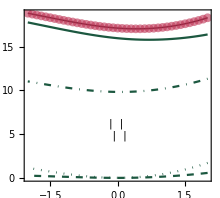

```mathematica
leg=Multicolumn[{LineLegend[{Black},{MaTeX["\\sigma",FontSize->15]}],
PointLegend[{magentaviva},{MaTeX["\\sigma_\\text{ti}",FontSize->15]},LegendMarkers->(mark[[1]])],LineLegend[{Dashed,castletongreen},{MaTeX["\\sigma_\\text{zk}^{(1)}",FontSize->15]},LegendMarkerSize->22],LineLegend[{Dotted,castletongreen},{MaTeX["\\sigma_\\text{zk}^{(2)}",FontSize->15]},LegendMarkerSize->22],
LineLegend[{DotDashed,castletongreen},{MaTeX["\\sigma_\\text{zk}^{(3)}",FontSize->15]},LegendMarkerSize->22],
LineLegend[{castletongreen},{MaTeX["\\sigma_\\text{zk}^{(4)}",FontSize->15]},LegendMarkerSize->22]},3,Spacings->{0,-1}];
plotDDEPR=Show[
ListLinePlot[{#1,#3}&@@@vec,PlotStyle->{Black,Thick},PlotRange->All],
ListPlot[{#1,#5}&@@@vec,PlotStyle->{magentaviva,Opacity[.6]},PlotMarkers->{mark[[1]],9}],
ListLinePlot[{#1,Total[#4[[;;2]]]}&@@@vec,PlotStyle->{castletongreen,Dashed}],
ListLinePlot[{#1,Total[#4[[;;4]]]}&@@@vec,PlotStyle->{castletongreen,Dotted}],
ListLinePlot[{#1,Total[#4[[;;6]]]}&@@@vec,PlotStyle->{castletongreen,DotDashed}],
ListLinePlot[{#1,Total[#4[[;;8]]]}&@@@vec,PlotStyle->{castletongreen}],
Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["A_{12}",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.5,.3}]]},ImageSize->220,AspectRatio->0.9,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->{{-2,2},All},ImagePadding->{{17,5},{40,5}}]
```

```mathematica
{Γ1,Γ2,Γ3,Γ4}={11,5,7,13};
{μ1,μ2,μ3,μ4}={5,1,6,1};
{β1,β2,β3,β4}={1,1,1,1};
{ϵu,ϵd,Δϵ}={2,1,3};
vec2={};Do[
μ2=x;
w0111r3=Γ3 (1-FD[ϵd+Δϵ-μ3,β3]);w1101r3=Γ3 FD[ϵd+Δϵ-μ3,β3];
w0111r4=Γ4 (1-FD[ϵd+Δϵ-μ4,β4]);w1101r4=Γ4 FD[ϵd+Δϵ-μ4,β4];
w0100r1=Γ1 FD[ϵu-μ1,β1];w0001r1=Γ1 (1-FD[ϵu-μ1,β1]);
w0100r2=Γ2 FD[ϵu-μ2,β2];w0001r2=Γ2 (1-FD[ϵu-μ2,β2]);
w1110r1=Γ1 FD[ϵu+Δϵ-μ1,β1];w1011r1=Γ1(1- FD[ϵu+Δϵ-μ1,β1]);
w1110r2=Γ2 FD[ϵu+Δϵ-μ2,β2];w1011r2=Γ2(1- FD[ϵu+Δϵ-μ2,β2]);
w1000r3=Γ3 FD[ϵd-μ3,β3];w0010r3=Γ3 (1-FD[ϵd-μ3,β3]);
w1000r4=Γ4 FD[ϵd-μ4,β4];w0010r4=Γ4 (1-FD[ϵd-μ4,β4]);
(*01,11,10,00*)
R=({{0, w0111r3+w0111r4, 0, w0100r1+w0100r2}, {w1101r3+w1101r4, 0, w1110r1+w1110r2, 0}, {0, w1011r1+w1011r2, 0, w1000r3+w1000r4}, {w0001r1+w0001r2, 0, w0010r3+w0010r4, 0}});
R=(R-DiagonalMatrix[Total[R]]);pss=SteadyState[R];
x1plus={{4,1,w0100r1},{3,2,w1110r1}};x1minus={{1,4,w0001r1},{2,3,w1011r1}};rev[x1plus]=x1minus;rev[x1minus]=x1plus;
x2plus={{4,1,w0100r2},{3,2,w1110r2}};x2minus={{1,4,w0001r2},{2,3,w1011r2}};rev[x2plus]=x2minus;rev[x2minus]=x2plus;
x3plus={{4,3,w1000r3},{1,2,w1101r3}};x3minus={{3,4,w0010r3},{2,1,w0111r3}};rev[x3plus]=x3minus;rev[x3minus]=x3plus;
x4plus={{4,3,w1000r4},{1,2,w1101r4}};x4minus={{3,4,w0010r4},{2,1,w0111r4}};rev[x4plus]=x4minus;rev[x4minus]=x4plus;
Xspace={x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus};
transitions={{{4,1,w0100r1},{1,4,w0001r1}},{{4,1,w0100r2},{1,4,w0001r2}},{{3,2,w1110r1},{2,3,w1011r1}},{{3,2,w1110r2},{2,3,w1011r2}},{{1,2,w1101r3},{2,1,w0111r3}},{{1,2,w1101r4},{2,1,w0111r4}},{{4,3,w1000r3},{3,4,w0010r3}},{{4,3,w1000r4},{3,4,w0010r4}}};
σ=N@EPR[R,transitions];
S=Smatrix[R,Xspace];Z=N@Kfun[Xspace,pss];

(*σzk*)
σzk=Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace;

(*σti*)
A12=β1 μ1-β2 μ2;A34=β3 μ3-β4 μ4;
a12empirical=Log[(Px2Gx1[pss,Xspace,R][x1plus,x2minus]Px[pss,Xspace,R][x1plus])/(Px2Gx1[pss,Xspace,R][x2plus,x1minus]Px[pss,Xspace,R][x2plus])];
a34empirical=Log[(Px2Gx1[pss,Xspace,R][x3plus,x4minus]Px[pss,Xspace,R][x3plus])/(Px2Gx1[pss,Xspace,R][x4plus,x3minus]Px[pss,Xspace,R][x4plus])];
σti=Z(Px[pss,Xspace,R][x1plus]-Px[pss,Xspace,R][x1minus])a12empirical+Z(Px[pss,Xspace,R][x3plus]-Px[pss,Xspace,R][x3minus])a34empirical;

(*observing reservoir 1*)
trans1={x1plus,x1minus};
Dx=0;Dtt=0;
Do[
Px1x2=Px2Gx1[pss,trans1,R][x1,x2]Px[pss,trans1,R][x1];
Px2rx1r=Px2Gx1[pss,trans1,R][rev[x2],rev[x1]]Px[pss,trans1,R][rev[x2]];
a=Px2Gx1[pss,trans1,R][x1,x2]//Simplify//Chop;
b=Px2Gx1[pss,trans1,R][rev[x2],rev[x1]]//Simplify//Chop;
at=If[PossibleZeroQ[a],∞,(Px2tGx1[pss,trans1,R][x1,x2,t])/a//Simplify//Chop];
bt=If[PossibleZeroQ[b],∞,(Px2tGx1[pss,trans1,R][rev[x2],rev[x1],t])/b//Simplify//Chop];
Dx+=Px1x2 SmartLog[Px1x2,Px2rx1r];
Dtt+=If[PossibleZeroQ[a]∨PossibleZeroQ[b],0,Px1x2 Quiet@NIntegrate[at SmartLog[at,bt],{t,0,∞}]];
,{x1,Xspace[[;;2]]},{x2,Xspace[[;;2]]}];

AppendTo[vec2,Chop@{A12,A34,σ,σzk,σti,Dx,Dtt}];
,{x,4.5,5.5,.025}]
```

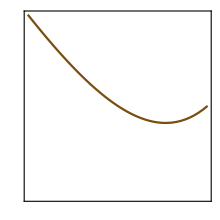
{-Graphics--Graphics-,-Graphics-}

```mathematica
size=220;ar=1;
leg=Column[{LineLegend[{pageantblue,sepia},MaTeX[#,FontSize->14]&/@{"D_x","D_t\\ [10^{-4}]"}]},Automatic,-.3];
plot1=ListLinePlot[{#1,#6}&@@@vec2,PlotStyle->pageantblue,ImagePadding->{{22,20},{40,5}},Axes->False,Frame->{True,True,True,False},FrameStyle->{Black,pageantblue,Black,Black},ImageSize->size,AspectRatio->ar,LabelStyle->{Black,FontFamily->"Times"},FrameLabel->{MaTeX["A_{12}",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.6,.77}]]}];
plot2=ListLinePlot[{#1,#7 10^4}&@@@vec2,PlotStyle->sepia,ImagePadding->{{22,20},{40,5}},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Black,Black,Black,sepia},ImageSize->size,AspectRatio->ar,LabelStyle->{Black,FontFamily->"Times"},FrameLabel->{MaTeX["A_{12}",FontSize->14],""}];
plotDDD=Overlay[{plot1,plot2}];
{plotDDD,plotDDEPR}
```

```mathematica
Export["plot_DD_EPR.png",plotDDEPR,"PNG",ImageResolution->600]
Export["plot_DD_Dxt.png",plotDDD,"PNG",ImageResolution->600]
```

plot_DD_EPR.png

plot_DD_Dxt.png

## DQD with a hidden hop

```mathematica
{Γ1,Γ2,Γ3,Γ4,Γ5}={11,5,7,13,6};
{μ1,μ2,μ3,μ4}={5,1,6,1};
{β1,β2,β3,β4,β5}={1,1,1,1,1};
{ϵu,ϵd,Δϵ}={2,1,3};
vec={};Do[
Γ5=x;
w0111r3=Γ3 (1-FD[ϵd+Δϵ-μ3,β3]);w1101r3=Γ3 FD[ϵd+Δϵ-μ3,β3];
w0111r4=Γ4 (1-FD[ϵd+Δϵ-μ4,β4]);w1101r4=Γ4 FD[ϵd+Δϵ-μ4,β4];
w0100r1=Γ1 FD[ϵu-μ1,β1];w0001r1=Γ1 (1-FD[ϵu-μ1,β1]);
w0100r2=Γ2 FD[ϵu-μ2,β2];w0001r2=Γ2 (1-FD[ϵu-μ2,β2]);
w1110r1=Γ1 FD[ϵu+Δϵ-μ1,β1];w1011r1=Γ1(1- FD[ϵu+Δϵ-μ1,β1]);
w1110r2=Γ2 FD[ϵu+Δϵ-μ2,β2];w1011r2=Γ2(1- FD[ϵu+Δϵ-μ2,β2]);
w1000r3=Γ3 FD[ϵd-μ3,β3];w0010r3=Γ3 (1-FD[ϵd-μ3,β3]);
w1000r4=Γ4 FD[ϵd-μ4,β4];w0010r4=Γ4 (1-FD[ϵd-μ4,β4]);
w1001=Γ5 BE[ϵu-ϵd,β5];w0110=Γ5(1+BE[ϵu-ϵd,β5]);
(*01,11,10,00*)
R=({{0, w0111r3+w0111r4, w0110, w0100r1+w0100r2}, {w1101r3+w1101r4, 0, w1110r1+w1110r2, 0}, {w1001, w1011r1+w1011r2, 0, w1000r3+w1000r4}, {w0001r1+w0001r2, 0, w0010r3+w0010r4, 0}});
R=(R-DiagonalMatrix[Total[R]]);pss=SteadyState[R];
x1plus={{4,1,w0100r1},{3,2,w1110r1}};x1minus={{1,4,w0001r1},{2,3,w1011r1}};rev[x1plus]=x1minus;rev[x1minus]=x1plus;
x2plus={{4,1,w0100r2},{3,2,w1110r2}};x2minus={{1,4,w0001r2},{2,3,w1011r2}};rev[x2plus]=x2minus;rev[x2minus]=x2plus;
x3plus={{4,3,w1000r3},{1,2,w1101r3}};x3minus={{3,4,w0010r3},{2,1,w0111r3}};rev[x3plus]=x3minus;rev[x3minus]=x3plus;
x4plus={{4,3,w1000r4},{1,2,w1101r4}};x4minus={{3,4,w0010r4},{2,1,w0111r4}};rev[x4plus]=x4minus;rev[x4minus]=x4plus;
Xspace={x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus};
transitions={{{4,1,w0100r1},{1,4,w0001r1}},{{4,1,w0100r2},{1,4,w0001r2}},{{3,2,w1110r1},{2,3,w1011r1}},{{3,2,w1110r2},{2,3,w1011r2}},{{1,2,w1101r3},{2,1,w0111r3}},{{1,2,w1101r4},{2,1,w0111r4}},{{4,3,w1000r3},{3,4,w0010r3}},{{4,3,w1000r4},{3,4,w0010r4}},{{3,1,w0110},{1,3,w1001}}};
σ=N@EPR[R,transitions];
S=Smatrix[R,Xspace];Z=N@Kfun[Xspace,pss];

(*σzk*)
σzk=Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace;

AppendTo[vec,Chop@{x,σ,σzk}];
,{x,0,5,.1}]
```

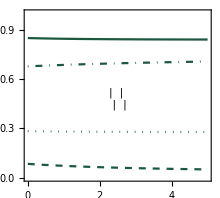

```mathematica
leg=Multicolumn[{LineLegend[{Dashed,castletongreen},{MaTeX["\\sigma_\\text{zk}^{(1)}",FontSize->15]},LegendMarkerSize->22],LineLegend[{Dotted,castletongreen},{MaTeX["\\sigma_\\text{zk}^{(2)}",FontSize->15]},LegendMarkerSize->22],
LineLegend[{DotDashed,castletongreen},{MaTeX["\\sigma_\\text{zk}^{(3)}",FontSize->15]},LegendMarkerSize->22],
LineLegend[{castletongreen},{MaTeX["\\sigma_\\text{zk}^{(4)}",FontSize->15]},LegendMarkerSize->22]},3,Spacings->{0,-1}];
plotDDEPR=Show[
ListLinePlot[{#1,Total[#3[[;;2]]]/#2}&@@@vec,PlotStyle->{castletongreen,Dashed}],
ListLinePlot[{#1,Total[#3[[;;4]]]/#2}&@@@vec,PlotStyle->{castletongreen,Dotted}],
ListLinePlot[{#1,Total[#3[[;;6]]]/#2}&@@@vec,PlotStyle->{castletongreen,DotDashed}],
ListLinePlot[{#1,Total[#3[[;;8]]]/#2}&@@@vec,PlotStyle->{castletongreen}],
Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["\\Gamma_5",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.5,.48}]]},ImageSize->220,AspectRatio->0.9,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->{{0,5},{0,1}},ImagePadding->{{17,5},{40,5}}]
```

## Brusselator

### analytical results - summary

The state space is truncated with a fixed N_max and all other calculations are analytical

```mathematica
Nmax=20;Nx[Nmax_][i_]:=Floor[(i-1)/(Nmax+1)];Ny[Nmax_][i_]:=Mod[i-1,Nmax+1];
{k1,km1,k2,km2,k3,km3}={1,2,3,3,2,5};{A,B}={5,15};V=10;
(*{k1,km1,k2,km2,k3,km3}={"k1","km1","k2","km2","k3","km3"};{A,B}={"A","B"};V="V";*)
```

Builiding the generator:

```mathematica
(*yp = +B, xp = -A, y = inner*)
ruleyp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[k2 B],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruleym=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[km2 Ny[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[k1 A],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexm=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[km1 Nx[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulex=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[km3(Nx[Nmax][j](Nx[Nmax][j]-1)(Nx[Nmax][j]-2))/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruley=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[k3(Nx[Nmax][j](Nx[Nmax][j]-1)Ny[Nmax][j])/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
Rsp1=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley]];
TRsp=Total[Rsp1];
ruleesc=Table[{i,i}->-TRsp[[i]],{i,(Nmax+1)^2}];
Rsp=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley,ruleesc]];
ByteCount[Rsp]/10^6//N
```

0.051312

Stationary distribution

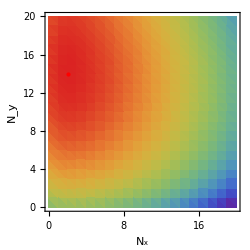
{-Graphics-,-Graphics3D-}

```mathematica
<<ComputationalGeometry`
pss=SteadyState[Rsp];
pssNxNy=Table[{Nx[Nmax][i],Ny[Nmax][i],pss[[i]]},{i,Length@pss}];
points={#1,#2}&@@@pssNxNy;zval=#3&@@@pssNxNy;
tri=DelaunayTriangulation[points];
tests=And@@Thread[zval[[#1]]>zval[[#2]]]&@@@tri;
maxima=Pick[points,tests];
{ListDensityPlot[ArrayFlatten[{{points,List/@zval}}],Epilog->{Red,PointSize[Large],Point[maxima]},PlotRange->All,ImageSize->250,FrameStyle->Black,FrameLabel->{"N_x","N_y"},ColorFunction->"Rainbow",ScalingFunctions->{None,None,"Log"}],ListPlot3D[pssNxNy,PlotRange->All,AxesLabel->{"N_x","N_y","p_st"},ImageSize->300,AxesStyle->Black]}
```

Defining the multifilar events

```mathematica
(*yp = +B, xp = +A, y = inner*)
xAplus={#1[[2]],#1[[1]],#2}&@@@rulexp;xAminus={#1[[2]],#1[[1]],#2}&@@@rulexm;rev[xAplus]=xAminus;rev[xAminus]=xAplus;
xBplus={#1[[2]],#1[[1]],#2}&@@@ruleyp;xBminus={#1[[2]],#1[[1]],#2}&@@@ruleym;rev[xBplus]=xBminus;rev[xBminus]=xBplus;
xIplus={#1[[2]],#1[[1]],#2}&@@@ruley;xIminus={#1[[2]],#1[[1]],#2}&@@@rulex;rev[xIplus]=xIminus;rev[xIminus]=xIplus;
Xspace={xAplus,xAminus,xBplus,xBminus,xIplus,xIminus};
transitions=Join[Transpose[{xAplus,xAminus}],Transpose[{xBplus,xBminus}],Transpose[{xIplus,xIminus}]];
Ssp=Smatrix[Rsp,transitions];
Z=Kfun[transitions,pss];
σ=EPR[Rsp,transitions];
```

The estimator σ_zk when chemostats A and B are monitored:

```mathematica
(*from A and B*)
transAB=Join[Transpose[{xAplus,xAminus}],Transpose[{xBplus,xBminus}]];
Ssp=Smatrix[Rsp,transAB];
Z=Kfun[transAB,pss];
σzk=Total[Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace[[;;4]]];
{σ,σzk}
```

{0.854994,0.196575}

The detector D_x and D_t

```mathematica
(*observing chemostats A and B*)
trans1={xAplus,xAminus,xBplus,xBminus};
Dx=0;Dtt=0;
time=AbsoluteTiming@Do[
Px1x2=Px2Gx1[pss,trans1,Rsp][x1,x2]Px[pss,trans1,Rsp][x1];
Px2rx1r=Px2Gx1[pss,trans1,Rsp][rev[x2],rev[x1]]Px[pss,trans1,Rsp][rev[x2]];
a=Px2Gx1[pss,trans1,Rsp][x1,x2]//Simplify//Chop;
b=Px2Gx1[pss,trans1,Rsp][rev[x2],rev[x1]]//Simplify//Chop;
at=If[PossibleZeroQ[a],∞,(Px2tGx1[pss,trans1,Rsp][x1,x2,t])/a//Expand];
bt=If[PossibleZeroQ[b],∞,(Px2tGx1[pss,trans1,Rsp][rev[x2],rev[x1],t])/b//Expand];
Dx+=Px1x2 SmartLog[Px1x2,Px2rx1r];
Dtt+=If[PossibleZeroQ[a]∨PossibleZeroQ[b],0,Px1x2 Quiet@NIntegrate[at SmartLog[at,bt],{t,0,∞}]];
,{x1,Xspace[[;;4]]},{x2,Xspace[[;;4]]}];
Print[ToString[time[[1]]/60]<>" minutes"]
```

0.00160208 minutes

```mathematica
{Dx,Dtt}
```

{0.00415503,1.37694×10^-6}

```mathematica
time[[1]]/60
```

7.75259

```mathematica
Ca={xAminus,xBplus,xIplus};
A1=Log[(Px2Gx1[pss,Xspace,Rsp][Ca[[2]],Ca[[3]]]Px2Gx1[pss,Xspace,Rsp][Ca[[1]],Ca[[2]]]Px[pss,Xspace,Rsp][Ca[[1]]])/(Px2Gx1[pss,Xspace,Rsp][rev[Ca[[2]]],rev[Ca[[1]]]]Px2Gx1[pss,Xspace,Rsp][rev[Ca[[3]]],rev[Ca[[2]]]]Px[pss,Xspace,Rsp][rev[Ca[[3]]]])];
Ca={xIplus,xAminus,xBplus};
A2=Log[(Px2Gx1[pss,Xspace,Rsp][Ca[[2]],Ca[[3]]]Px2Gx1[pss,Xspace,Rsp][Ca[[1]],Ca[[2]]]Px[pss,Xspace,Rsp][Ca[[1]]])/(Px2Gx1[pss,Xspace,Rsp][rev[Ca[[2]]],rev[Ca[[1]]]]Px2Gx1[pss,Xspace,Rsp][rev[Ca[[3]]],rev[Ca[[2]]]]Px[pss,Xspace,Rsp][rev[Ca[[3]]]])];
Ca={xBplus,xIplus,xAminus};
A3=Log[(Px2Gx1[pss,Xspace,Rsp][Ca[[2]],Ca[[3]]]Px2Gx1[pss,Xspace,Rsp][Ca[[1]],Ca[[2]]]Px[pss,Xspace,Rsp][Ca[[1]]])/(Px2Gx1[pss,Xspace,Rsp][rev[Ca[[2]]],rev[Ca[[1]]]]Px2Gx1[pss,Xspace,Rsp][rev[Ca[[3]]],rev[Ca[[2]]]]Px[pss,Xspace,Rsp][rev[Ca[[3]]]])];
```

```mathematica
JA=Z(Px[pss,Xspace,Rsp][xAminus]-Px[pss,Xspace,Rsp][xAplus]);
JB=Z(Px[pss,Xspace,Rsp][xBplus]-Px[pss,Xspace,Rsp][xBminus]);
JI=Z(Px[pss,Xspace,Rsp][xIplus]-Px[pss,Xspace,Rsp][xIminus]);
```

```mathematica
Δμ=Log[(B k2 km1 k3)/(A km2 k1 km3)]//N;
{σ,Mean[{JA A1,JA A2,JA A3}]}
```

{0.896544,0.787922}

### analytical plot

The state space is truncated with a fixed N_max and all other calculations are analytical

```mathematica
Nmax=20;Nx[Nmax_][i_]:=Floor[(i-1)/(Nmax+1)];Ny[Nmax_][i_]:=Mod[i-1,Nmax+1];
{k1,km1,k2,km2,k3,km3}={1,2,3,3,2,5};{A,B}={5,15};V=10;
vec={};time=AbsoluteTiming@Do[
ruleyp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[k2 B],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruleym=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[km2 Ny[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[k1 A],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexm=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[km1 Nx[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulex=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[km3(Nx[Nmax][j](Nx[Nmax][j]-1)(Nx[Nmax][j]-2))/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruley=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[k3(Nx[Nmax][j](Nx[Nmax][j]-1)Ny[Nmax][j])/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
Rsp1=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley]];
TRsp=Total[Rsp1];
ruleesc=Table[{i,i}->-TRsp[[i]],{i,(Nmax+1)^2}];
Rsp=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley,ruleesc]];
pss=SteadyState[Rsp];
xAplus={#1[[2]],#1[[1]],#2}&@@@rulexp;xAminus={#1[[2]],#1[[1]],#2}&@@@rulexm;rev[xAplus]=xAminus;rev[xAminus]=xAplus;
xBplus={#1[[2]],#1[[1]],#2}&@@@ruleyp;xBminus={#1[[2]],#1[[1]],#2}&@@@ruleym;rev[xBplus]=xBminus;rev[xBminus]=xBplus;
xIplus={#1[[2]],#1[[1]],#2}&@@@ruley;xIminus={#1[[2]],#1[[1]],#2}&@@@rulex;rev[xIplus]=xIminus;rev[xIminus]=xIplus;
Xspace={xAplus,xAminus,xBplus,xBminus,xIplus,xIminus};
transitions=Join[Transpose[{xAplus,xAminus}],Transpose[{xBplus,xBminus}],Transpose[{xIplus,xIminus}]];
Z=Kfun[transitions,pss];
σ=EPR[Rsp,transitions];

(*from A and B*)
transAB=Xspace[[;;4]];
ZAB=Kfun[transAB,pss];
σzk=Total[Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@transAB];

(*Dx and Dt from A and B*)
Dx=0;Dtt=0;
Do[
Px1x2=Px2Gx1[pss,transAB,Rsp][x1,x2]Px[pss,transAB,Rsp][x1];
Px2rx1r=Px2Gx1[pss,transAB,Rsp][rev[x2],rev[x1]]Px[pss,transAB,Rsp][rev[x2]];
a=Px2Gx1[pss,transAB,Rsp][x1,x2]//Simplify//Chop;
b=Px2Gx1[pss,transAB,Rsp][rev[x2],rev[x1]]//Simplify//Chop;
at=If[PossibleZeroQ[a],∞,(Px2tGx1[pss,transAB,Rsp][x1,x2,t])/a//Expand];
bt=If[PossibleZeroQ[b],∞,(Px2tGx1[pss,transAB,Rsp][rev[x2],rev[x1],t])/b//Expand];
Dx+=Px1x2 SmartLog[Px1x2,Px2rx1r];
Dtt+=If[PossibleZeroQ[a]∨PossibleZeroQ[b],0,Px1x2 Quiet@NIntegrate[at SmartLog[at,bt],{t,0,∞}]];
,{x1,Xspace[[;;4]]},{x2,Xspace[[;;4]]}];

(*approximation*)
Ca={xAminus,xBplus,xIplus};
A1=Log[(Px2Gx1[pss,Xspace,Rsp][Ca[[2]],Ca[[3]]]Px2Gx1[pss,Xspace,Rsp][Ca[[1]],Ca[[2]]]Px[pss,Xspace,Rsp][Ca[[1]]])/(Px2Gx1[pss,Xspace,Rsp][rev[Ca[[2]]],rev[Ca[[1]]]]Px2Gx1[pss,Xspace,Rsp][rev[Ca[[3]]],rev[Ca[[2]]]]Px[pss,Xspace,Rsp][rev[Ca[[3]]]])];
Ca={xIplus,xAminus,xBplus};
A2=Log[(Px2Gx1[pss,Xspace,Rsp][Ca[[2]],Ca[[3]]]Px2Gx1[pss,Xspace,Rsp][Ca[[1]],Ca[[2]]]Px[pss,Xspace,Rsp][Ca[[1]]])/(Px2Gx1[pss,Xspace,Rsp][rev[Ca[[2]]],rev[Ca[[1]]]]Px2Gx1[pss,Xspace,Rsp][rev[Ca[[3]]],rev[Ca[[2]]]]Px[pss,Xspace,Rsp][rev[Ca[[3]]]])];
Ca={xBplus,xIplus,xAminus};
A3=Log[(Px2Gx1[pss,Xspace,Rsp][Ca[[2]],Ca[[3]]]Px2Gx1[pss,Xspace,Rsp][Ca[[1]],Ca[[2]]]Px[pss,Xspace,Rsp][Ca[[1]]])/(Px2Gx1[pss,Xspace,Rsp][rev[Ca[[2]]],rev[Ca[[1]]]]Px2Gx1[pss,Xspace,Rsp][rev[Ca[[3]]],rev[Ca[[2]]]]Px[pss,Xspace,Rsp][rev[Ca[[3]]]])];
JA=Z(Px[pss,Xspace,Rsp][xAminus]-Px[pss,Xspace,Rsp][xAplus]);
JB=Z(Px[pss,Xspace,Rsp][xBplus]-Px[pss,Xspace,Rsp][xBminus]);
JI=Z(Px[pss,Xspace,Rsp][xIplus]-Px[pss,Xspace,Rsp][xIminus]);

AppendTo[vec,{A,Log[(B k2 km1 k3)/(A km2 k1 km3)]//N,σ,σzk,Dx,Dtt,A1,A2,A3,JA,JB,JI}];
,{A,5,7,1}];
Print[ToString[time[[1]]/60]<>" minutes"]
vec
```

24.4328 minutes

{{5,0.875469,0.854994,0.196575,0.00415503,1.37694×10^-6,0.685543,0.837223,0.901508,0.976612,0.976612,0.976612},{6,0.693147,0.738086,0.200522,0.00414174,1.08875×10^-6,0.557816,0.660855,0.714107,1.06483,1.06483,1.06483},{7,0.538997,0.573978,0.177365,0.00358659,7.66102×10^-7,0.443708,0.512882,0.555452,1.0649,1.0649,1.0649}}

```mathematica
res={{5,0.8754687373538999,0.8549935030025505,0.19657476711349087,0.00415503143705734,1.3769447089326433*^-6,0.6855431663395439,0.837223243463029,0.9015080161587424,0.976612260977774,0.9766122609777748,0.9766122609777694},{6,0.6931471805599453,0.7380858909026418,0.20052248724516353,0.004141741756133155,1.0887543030497657*^-6,0.557815702876093,0.6608553404968258,0.7141067658344372,1.064832854555353,1.0648328545553456,1.0648328545553498},{7,0.5389965007326869,0.5739779423285962,0.17736487831553227,0.0035865907984318768,7.661015040179675*^-7,0.4437077486729093,0.5128817201702516,0.5554524467813396,1.0649010551058158,1.064901055105834,1.064901055105818},{20,-0.5108256237659907,1.8850289619722111,1.065239231241517,0.01755441891092044,2.56428455647781*^-6,-0.4723526708297562,-0.4864294729982581,-0.5254897283120619,-3.690161327607409,-3.6901613276073673,-3.6901613276073766}};
```

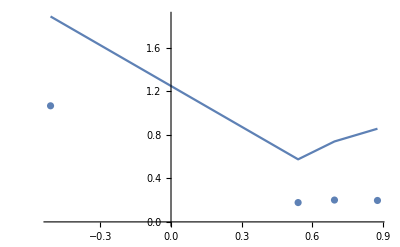

```mathematica
Show[{ListLinePlot[{#2,#3}&@@@res],ListPlot[{#2,#4}&@@@res]}]
```

### change with N

```mathematica
Nmax=20;Nx[Nmax_][i_]:=Floor[(i-1)/(Nmax+1)];Ny[Nmax_][i_]:=Mod[i-1,Nmax+1];
{k1,km1,k2,km2,k3,km3}={1,2,3,3,2,5};{A,B}={20,15};V=10;
vec2={};time=AbsoluteTiming@Do[
ruleyp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[k2 B],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruleym=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[km2 Ny[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[k1 A],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexm=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[km1 Nx[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulex=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[km3(Nx[Nmax][j](Nx[Nmax][j]-1)(Nx[Nmax][j]-2))/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruley=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[k3(Nx[Nmax][j](Nx[Nmax][j]-1)Ny[Nmax][j])/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
Rsp1=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley]];
TRsp=Total[Rsp1];
ruleesc=Table[{i,i}->-TRsp[[i]],{i,(Nmax+1)^2}];
Rsp=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley,ruleesc]];
pss=SteadyState[Rsp];
xAplus={#1[[2]],#1[[1]],#2}&@@@rulexp;xAminus={#1[[2]],#1[[1]],#2}&@@@rulexm;rev[xAplus]=xAminus;rev[xAminus]=xAplus;
xBplus={#1[[2]],#1[[1]],#2}&@@@ruleyp;xBminus={#1[[2]],#1[[1]],#2}&@@@ruleym;rev[xBplus]=xBminus;rev[xBminus]=xBplus;
xIplus={#1[[2]],#1[[1]],#2}&@@@ruley;xIminus={#1[[2]],#1[[1]],#2}&@@@rulex;rev[xIplus]=xIminus;rev[xIminus]=xIplus;
Xspace={xAplus,xAminus,xBplus,xBminus,xIplus,xIminus};
transitions=Join[Transpose[{xAplus,xAminus}],Transpose[{xBplus,xBminus}],Transpose[{xIplus,xIminus}]];
Z=Kfun[transitions,pss];
σ=EPR[Rsp,transitions];

(*from A and B*)
transAB=Xspace[[;;4]];
ZAB=Kfun[transAB,pss];
σzk=Total[Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@transAB];

(*Dx and Dt from A and B*)
(*Dx=0;Dtt=0;
Do[
Px1x2=Px2Gx1[pss,transAB,Rsp][x1,x2]Px[pss,transAB,Rsp][x1];
Px2rx1r=Px2Gx1[pss,transAB,Rsp][rev[x2],rev[x1]]Px[pss,transAB,Rsp][rev[x2]];
a=Px2Gx1[pss,transAB,Rsp][x1,x2]//Simplify//Chop;
b=Px2Gx1[pss,transAB,Rsp][rev[x2],rev[x1]]//Simplify//Chop;
at=If[PossibleZeroQ[a],∞,(Px2tGx1[pss,transAB,Rsp][x1,x2,t])/a//Expand];
bt=If[PossibleZeroQ[b],∞,(Px2tGx1[pss,transAB,Rsp][rev[x2],rev[x1],t])/b//Expand];
Dx+=Px1x2 SmartLog[Px1x2,Px2rx1r];
Dtt+=If[PossibleZeroQ[a]∨PossibleZeroQ[b],0,Px1x2 Quiet@NIntegrate[at SmartLog[at,bt],{t,0,∞}]];
,{x1,Xspace[[;;4]]},{x2,Xspace[[;;4]]}];

(*approximation*)
Ca={xAminus,xBplus,xIplus};
A1=Log[(Px2Gx1[pss,Xspace,Rsp][Ca[[2]],Ca[[3]]]Px2Gx1[pss,Xspace,Rsp][Ca[[1]],Ca[[2]]]Px[pss,Xspace,Rsp][Ca[[1]]])/(Px2Gx1[pss,Xspace,Rsp][rev[Ca[[2]]],rev[Ca[[1]]]]Px2Gx1[pss,Xspace,Rsp][rev[Ca[[3]]],rev[Ca[[2]]]]Px[pss,Xspace,Rsp][rev[Ca[[3]]]])];
Ca={xIplus,xAminus,xBplus};
A2=Log[(Px2Gx1[pss,Xspace,Rsp][Ca[[2]],Ca[[3]]]Px2Gx1[pss,Xspace,Rsp][Ca[[1]],Ca[[2]]]Px[pss,Xspace,Rsp][Ca[[1]]])/(Px2Gx1[pss,Xspace,Rsp][rev[Ca[[2]]],rev[Ca[[1]]]]Px2Gx1[pss,Xspace,Rsp][rev[Ca[[3]]],rev[Ca[[2]]]]Px[pss,Xspace,Rsp][rev[Ca[[3]]]])];
Ca={xBplus,xIplus,xAminus};
A3=Log[(Px2Gx1[pss,Xspace,Rsp][Ca[[2]],Ca[[3]]]Px2Gx1[pss,Xspace,Rsp][Ca[[1]],Ca[[2]]]Px[pss,Xspace,Rsp][Ca[[1]]])/(Px2Gx1[pss,Xspace,Rsp][rev[Ca[[2]]],rev[Ca[[1]]]]Px2Gx1[pss,Xspace,Rsp][rev[Ca[[3]]],rev[Ca[[2]]]]Px[pss,Xspace,Rsp][rev[Ca[[3]]]])];
JA=Z(Px[pss,Xspace,Rsp][xAminus]-Px[pss,Xspace,Rsp][xAplus]);
JB=Z(Px[pss,Xspace,Rsp][xBplus]-Px[pss,Xspace,Rsp][xBminus]);
JI=Z(Px[pss,Xspace,Rsp][xIplus]-Px[pss,Xspace,Rsp][xIminus]);*)

AppendTo[vec2,{Nmax,σ,σzk}];
,{Nmax,5,30,5}];
Print[ToString[time[[1]]/60]<>" minutes"]
```

0.844486 minutes

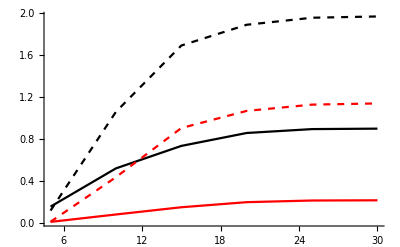

```mathematica
Show[ListLinePlot[{{#1,#2}&@@@vec,{#1,#3}&@@@vec},PlotStyle->{Black,Red}],ListLinePlot[{{#1,#2}&@@@vec2,{#1,#3}&@@@vec2},PlotStyle->{{Black,Dashed},{Red,Dashed}}],PlotRange->All]
```

```mathematica
{Log[(B k2 km1 k3)/(5 km2 k1 km3)],Log[(B k2 km1 k3)/(20 km2 k1 km3)]}//N
```

{0.875469,-0.510826}

### plot

#### from simulations

```mathematica
eprvec=ToExpression@StringReplace["[[0.8754687373538999,3.9069883991760728,0.11352164343679916],[0.780158557549575,3.320680897707225,0.08749683832636729],[0.6931471805599453,2.7862934218653193,0.06850669301544057],[0.613104472886409,2.3113645939663616,0.08087591388823372],[0.5389965007326869,1.8566081539801076,0.05173634806936412],[0.47000362924573563,1.4584528796789102,0.05515733293624269],[0.4054651081081644,1.1447252279615536,0.03428196571850025],[0.3448404862917296,0.8315422986451353,0.049124594260152546],[0.2876820724517809,0.6092484244800086,0.03831420282806739],[0.2336148511815051,0.4246093446185636,0.030428441756299236],[0.1823215567939546,0.25616364197837493,0.02042163260503382],[0.13353139262452254,0.14393343180460078,0.013723056119743166],[0.0870113769896297,0.06322128636895183,0.012321593687937197],[0.0425596144187959,0.015792323694690368,0.005284577348954056],[0.0,0.0004257613291966253,0.001399908059670749],[-0.040821994520255166,0.014690435605700394,0.0056546764411799545],[-0.08004270767353637,0.0588956334830112,0.011148063521216282],[-0.11778303565638351,0.13393563428009841,0.01403736280661893],[-0.15415067982725836,0.23281280158947298,0.017364466998356625],[-0.18924199963852842,0.3445084894730673,0.02479609049710682],[-0.22314355131420968,0.4886963928375095,0.03066334682236052],[-0.25593337413720063,0.6543182663311053,0.034225325948882],[-0.2876820724517809,0.8494185997901151,0.04476896671674186],[-0.3184537311185346,1.0688211218973422,0.036786634329417006],[-0.3483066942682157,1.2824489572057938,0.04609068159890125],[-0.3772942311414681,1.5474513066779318,0.04745730086062685],[-0.40546510810816444,1.804251290870846,0.04591254822371138],[-0.43286408229627876,2.1106773312751628,0.0537404394619735],[-0.45953232937844024,2.39276052163039,0.048749585889290674],[-0.48550781578170077,2.7279931697975273,0.05287964871046262],[-0.5108256237659907,3.0692017005936805,0.06898424332971563]]",{"["->"{","]"->"}"}];
σzkvec=ToExpression@StringReplace["[[0.8754687373538999, 3.438126996430212, 0.19125229457033735], [0.780158557549575, 2.9673842054964314, 0.15612635376917597], [0.6931471805599453, 2.536648840683197, 0.123415827447259],
 [0.613104472886409, 2.1424014179259667, 0.14953112122889697], [0.5389965007326869, 1.7149236578118157, 0.09402428715923855], [0.47000362924573563, 1.3491783994844277, 0.10040412429815006],
 [0.4054651081081644, 1.0787305736265795, 0.06601660713065939],
 [0.3448404862917296, 0.7614041897483819, 0.08793348879073941],
 [0.2876820724517809, 0.5728543896938029, 0.07097138474949125],
 [0.2336148511815051, 0.41140497637745954, 0.05848312478701582],
 [0.1823215567939546, 0.23748901895490518, 0.039467799402070076],
 [0.13353139262452254, 0.13685228982743392, 0.02617298725016064],
 [0.0870113769896297, 0.06319221523534434, 0.025081333233070338],
 [0.0425596144187959, 0.017571444257147156, 0.009709029747386395],
 [0.0, 0.0011773436354943706, 0.0019404775723746485],
 [-0.040821994520255166, 0.01774158248969568, 0.010286669788051593],
 [-0.08004270767353637, 0.05839087354879301, 0.0202725031101826],
 [-0.11778303565638351, 0.13342685207328836, 0.02909262791329288],
 [-0.15415067982725836, 0.23023690001591887, 0.03502906608041418],
 [-0.18924199963852842, 0.329064301336029, 0.04587254673324172],
 [-0.22314355131420968, 0.46631879571330825, 0.059356746923351175],
 [-0.25593337413720063, 0.6245320829360529, 0.06647386454303283],
 [-0.2876820724517809, 0.8171893083803834, 0.08548296527380446],
 [-0.3184537311185346, 1.0370043792607087, 0.06998493305304887],
 [-0.3483066942682157, 1.2308180556450439, 0.08878571234514865],
 [-0.3772942311414681, 1.502574633774751, 0.0899377120960552],
 [-0.40546510810816444, 1.736427683189093, 0.09101681513686642],
 [-0.43286408229627876, 2.0538272764181777, 0.1057417505332396],
 [-0.45953232937844024, 2.3110608146894807, 0.09627922769824321],
 [-0.48550781578170077, 2.6475618966361987, 0.10204083611222624],
 [-0.5108256237659907, 2.9850367393031876, 0.13113731959026295]]",{"["->"{","]"->"}"}];
σtivec=ToExpression@StringReplace["[[0.8754687373538999, 3.9001472626486917, 0.2502431984632072],
 [0.780158557549575, 3.378331918091733, 0.2315622083901862],
 [0.6931471805599453, 2.7775170353186724, 0.22277702431196694],
 [0.613104472886409, 2.437128950014075, 0.28690736203492206],
 [0.5389965007326869, 1.943989331467876, 0.21629162576116193],
 [0.47000362924573563, 1.432244414063622, 0.18085801882881494],
 [0.4054651081081644, 1.142567712894829, 0.11346572852465583],
 [0.3448404862917296, 0.8135952065870009, 0.11853905978247911],
 [0.2876820724517809, 0.6318064632179804, 0.12250780158241678],
 [0.2336148511815051, 0.42998392418506864, 0.07460427234056359],
 [0.1823215567939546, 0.2720714739637382, 0.07992950619382429],
 [0.13353139262452254, 0.11559441255986995, 0.04377649626112145],
 [0.0870113769896297, 0.0575328661089082, 0.050060883558451535],
 [0.0425596144187959, 0.016203922584458626, 0.018897491396290416],
 [0.0, -0.00011549871055016128, 0.003483750209587156],
 [-0.040821994520255166, 0.013589179493611192, 0.015916665162862526],
 [-0.08004270767353637, 0.0706054366258613, 0.03906147978090375],
 [-0.11778303565638351, 0.12896995833232677, 0.05902071180971388],
 [-0.15415067982725836, 0.256302917687136, 0.07171377646192265],
 [-0.18924199963852842, 0.33233708287442526, 0.09402701398092761],
 [-0.22314355131420968, 0.4599035579083358, 0.09761047962115844],
 [-0.25593337413720063, 0.6752818344887195, 0.1657503481650977],
 [-0.2876820724517809, 0.8359980682701817, 0.13698904871093254],
 [-0.3184537311185346, 1.095939537122133, 0.15194460857985695],
 [-0.3483066942682157, 1.2427204613582379, 0.1526182934697331],
 [-0.3772942311414681, 1.628778494020019, 0.18367366308298042],
 [-0.40546510810816444, 1.8149703295283843, 0.19064170000408975],
 [-0.43286408229627876, 2.0511391704005266, 0.27937271341037984],
 [-0.45953232937844024, 2.332607317447407, 0.22882373793167704],
 [-0.48550781578170077, 2.7311422822195466, 0.3287972985899644],
 [-0.5108256237659907, 3.1532940154923246, 0.2647396783903346]]",{"["->"{","]"->"}"}];
eprvecinset=ToExpression@StringReplace["[[0.2876820724517809, 0.6156225342434676, 0.039442248626765035],
 [0.25489224962879004, 0.48634025163422223, 0.02527626791597167],
 [0.22314355131420976, 0.3813878855358773, 0.023578016151779648],
 [0.1923718926474561, 0.28040921866916363, 0.02091099663996237],
 [0.16251892949777494, 0.20308700671011684, 0.016094082666012987],
 [0.13353139262452254, 0.1401037589747124, 0.01640713586715465],
 [0.10536051565782614, 0.08605199128444731, 0.012442093373726449],
 [0.07796154146971192, 0.04827055081845626, 0.01028423042454345],
 [0.05129329438755048, 0.024366782123747467, 0.006603564663373953],
 [0.02531780798429, 0.005452569329151026, 0.003076967099650397],
 [0.0, 0.00010337646674986602, 0.0016445801090384932],
 [-0.024692612590371636, 0.005734748201260974, 0.0030729814470556466],
 [-0.048790164169432056, 0.02189487354021336, 0.006261112164606766],
 [-0.07232066157962615, 0.04578687019973323, 0.010266866322957808],
 [-0.09531017980432478, 0.08774243525481618, 0.01349080734867319],
 [-0.11778303565638351, 0.13418059619765937, 0.01628397076020282],
 [-0.13976194237515888, 0.1875843878944133, 0.01756455063067814],
 [-0.16126814759612226, 0.26153943909446276, 0.023200466090788636],
 [-0.18232155679395445, 0.3288898420118524, 0.020458041071465996],
 [-0.20294084399669013, 0.39757673542810185, 0.024867518861496407],
 [-0.22314355131420968, 0.49127217132698825, 0.026267686115269896]]",{"["->"{","]"->"}"}];
σzkvecinset=ToExpression@StringReplace["[[0.2876820724517809, 0.5844580711795583, 0.07523337506475837],
 [0.25489224962879004, 0.45776952550259364, 0.048369192824541794],
 [0.22314355131420976, 0.3612777412017634, 0.04323827268966056],
 [0.1923718926474561, 0.2584503659182635, 0.03813644659856418],
 [0.16251892949777494, 0.18617673311375682, 0.027141163327540536],
 [0.13353139262452254, 0.13045903969546183, 0.030884931828461082],
 [0.10536051565782614, 0.07907198051312794, 0.021630239579189713],
 [0.07796154146971192, 0.045520083471120895, 0.017805343537201507],
 [0.05129329438755048, 0.027547262185839094, 0.014166744970713562],
 [0.02531780798429, 0.006521237404344712, 0.005137064062552105],
 [0.0, 0.0018661497375564609, 0.0016624046251495052],
 [-0.024692612590371636, 0.007775677697455821, 0.005900305250475937],
 [-0.048790164169432056, 0.022744189869094697, 0.0130103515079692],
 [-0.07232066157962615, 0.04436536042719237, 0.018857410232709232],
 [-0.09531017980432478, 0.0897716144429035, 0.028792532650607546],
 [-0.11778303565638351, 0.1353448282667492, 0.03270227671013627],
 [-0.13976194237515888, 0.1831914725620916, 0.03483900954054657],
 [-0.16126814759612226, 0.26439338355225417, 0.04306372918362971],
 [-0.18232155679395445, 0.3227818287473453, 0.04058000492877361],
 [-0.20294084399669013, 0.3756203559661913, 0.04728626823399449],
 [-0.22314355131420968, 0.469460321873029, 0.048192956456105766]]",{"["->"{","]"->"}"}];
σtivecinset=ToExpression@StringReplace["[[0.2876820724517809, 0.5881611026744573, 0.11515459813606008],
 [0.25489224962879004, 0.508057928138496, 0.08081020157317902],
 [0.22314355131420976, 0.39522578758096844, 0.09620453782426304],
 [0.1923718926474561, 0.2792164454548672, 0.08128059616571828],
 [0.16251892949777494, 0.19927714124932566, 0.06982916520381495],
 [0.13353139262452254, 0.15641592016350292, 0.04732607037999841],
 [0.10536051565782614, 0.07877254964738853, 0.03240541241471328],
 [0.07796154146971192, 0.039413588638328986, 0.023310851158667587],
 [0.05129329438755048, 0.03731900635677159, 0.02889774386464245],
 [0.02531780798429, 0.012411266208024492, 0.010813286473223476],
 [0.0, 0.003131021685996093, 0.0069289382394629],
 [-0.024692612590371636, 0.004507188014501749, 0.013790911937996227],
 [-0.048790164169432056, 0.020264998539683186, 0.016778985577974942],
 [-0.07232066157962615, 0.04245955962849421, 0.029284117382932944],
 [-0.09531017980432478, 0.09607105497172357, 0.048508895786668456],
 [-0.11778303565638351, 0.1526549690612748, 0.05770007882501501],
 [-0.13976194237515888, 0.20117713113693547, 0.0622465181083774],
 [-0.16126814759612226, 0.2663073313857869, 0.0655556849858355],
 [-0.18232155679395445, 0.3502564167220198, 0.08143613152333584],
 [-0.20294084399669013, 0.4089615962109791, 0.10645307457726996],
 [-0.22314355131420968, 0.49665822086759287, 0.11403104623595874]]",{"["->"{","]"->"}"}];
σxt={{0.4054651081081644,0.000015988870694023008},{0.28768207245178085,6.919358135334834*^-6},{0.1823215567939546,2.406090067890331*^-6},{0.0870113769896297,4.773932948265465*^-7},{0.,-1.8284494398133934*^-18},{-0.08004270767353636,3.113687468254066*^-7},{-0.15415067982725836,1.0204033210310176*^-6},{-0.22314355131420976,1.8960523975104622*^-6},{-0.28768207245178085,2.8032856149872085*^-6},{-0.3483066942682158,3.6653968395897037*^-6},{-0.4054651081081644,4.441346325689303*^-6}};
```

```mathematica
MinMax[#2&@@@σxt]
```

{-1.82845×10^-18,0.0000159889}

#### analytical calculations (truncate Nmax = 25)

```mathematica
σxtvec={{0.8754687373538999,0.0002940784121424341,6.859877612774524*^-9},{0.6931471805599453,0.00016549630924736323,3.81284189841272*^-9},{0.5389965007326869,0.00008979428322802052,2.2078671751114085*^-9},{0.4054651081081644,0.00004567245948386805,1.2879017306601856*^-9},{0.28768207245178085,0.000020715034896761185,7.299623041410249*^-10},{0.1823215567939546,7.515394273456867*^-6,3.782360198256359*^-10},{0.0870113769896297,1.5499177533331504*^-6,1.5043626857561373*^-10},{0.,1.986873865251555*^-19,7.162197116556568*^-20},{-0.08004270767353636,1.0825580961182022*^-6,1.0087579713785054*^-10},{-0.15415067982725836,3.658496485686474*^-6,1.6950176725279273*^-10},{-0.22314355131420976,6.9973374404955695*^-6,2.1700222497718037*^-10},{-0.28768207245178085,0.000010632143416576906,2.5068488475724317*^-10},{-0.3483066942682158,0.000014268095521424686,2.7540915581619094*^-10},{-0.4054651081081644,0.00001772377230088965,2.944123932656573*^-10},{-0.45953232937844013,0.000020892816859352982,3.0983132071354574*^-10},{-0.5108256237659907,0.000023718576750434303,3.230454740631209*^-10}};
σzktiepr={{0.8754687373538999,3.34193808539894,3.925582060777442,3.9255820607774257},{0.6931471805599453,2.397207287935315,2.760515314435287,2.760515314434935},{0.5389965007326869,1.6150847579892122,1.833406330662669,1.8334063306626562},{0.4054651081081644,1.0005734153382857,1.123465089872612,1.1234650898725391},{0.28768207245178085,0.5445903757712853,0.6061651678806076,0.6061651678802781},{0.1823215567939546,0.23430799349079182,0.2589321381351543,0.2589321381355365},{0.0870113769896297,0.056754719690938975,0.06233935120383004,0.06233935120365537},{0.,3.158765100978618*^-29,0.,-6.150585685817435*^-14},{-0.08004270767353636,0.05344655131132601,0.058131582979154696,0.058131582979647406},{-0.15415067982725836,0.20779737510510435,0.2250942091669593,0.2250942091673235},{-0.22314355131420976,0.45491607087430985,0.4909875474886794,0.4909875474892142},{-0.28768207245178085,0.7876650562422531,0.8473209516916923,0.8473209516916883},{-0.3483066942682158,1.1997530611742446,1.2867499010193972,1.2867499010191998},{-0.4054651081081644,1.6856018120026526,1.802867004900353,1.8028670049007773},{-0.45953232937844013,2.240233313913806,2.390036254743712,2.3900362547430802},{-0.5108256237659907,2.8591760013198417,3.0432610696006277,3.0432610696008955}};
```

#### plot

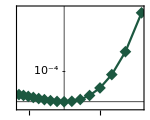

```mathematica
mark=#1&@@@Graphics`PlotMarkers[];
inset=
ListLinePlot[{#1,#2}&@@@σxtvec,PlotStyle->{castletongreen,Opacity[1]},PlotMarkers->{mark[[3]],12},
Frame->True,FrameStyle->Black,ImageSize->150,AspectRatio->.8,LabelStyle->{Black,FontFamily->"Times"},FrameTicks->{{None,None},{{-.4,0,.4,.8},None}},ScalingFunctions->{None,None},Epilog->Inset[Text[Style["10^-4 -",FontFamily->"Times"]],{-.16,1.02 10^-4}],Axes->False,GridLines->{{0},{0}},GridLinesStyle->Black,PlotRange->{All,{-2 10^-5,3.1 10^-4}}]
```

```mathematica
leg=Column[{LineLegend[{Black},{MaTeX["\\sigma",FontSize->15]}],
PointLegend[{magentaviva},MaTeX[#,FontSize->15]&/@{"\\sigma_\\text{ti}"},LegendMarkers->mark[[1]]],
PointLegend[{pageantblue},MaTeX[#,FontSize->15]&/@{"\\sigma_\\text{zk}"},LegendMarkers->mark[[2]]],
PointLegend[{castletongreen},MaTeX[#,FontSize->15]&/@{"\\sigma_{x,t}"},LegendMarkers->mark[[3]]]
},Automatic,-1];
p2=ListPlot[{#1,#3}&@@@σzktiepr,PlotStyle->{magentaviva,Opacity[.7]},PlotMarkers->{mark[[1]],12}];
p3=ListPlot[{#1,#2}&@@@σzktiepr,PlotStyle->{pageantblue,Opacity[.7]},PlotMarkers->{mark[[2]],12}];
p4=ListPlot[{#1,#2}&@@@σxtvec,PlotStyle->{castletongreen,Opacity[.7]},PlotMarkers->{mark[[3]],12}];
```

```mathematica
Show[{p1,p2,p3},PlotStyle->Black,Frame->True,FrameStyle->Black,PlotRange->{All,{0,4.5}},FrameLabel->{MaTeX["\\Delta\\mu",FontSize->15],""},Epilog->{Inset[leg,Scaled[{.18,.75}]],Inset[inset,Scaled[{.53,.72}],Automatic,.67]},ImageSize->250,AspectRatio->0.8,LabelStyle->{Black,FontFamily->"Times"},Axes->False]
```

-Graphics-

### verifications

```mathematica
{Log[(B k2 km1 k3)/(A km2 k1 km3)]//N,EPR[Rsp,transitions],Total[σzk]}
```

{0.875469,3.92888,3.34618}

```mathematica
(*σti*)
lα={xAminus,xBplus,xIplus};lαr=rev[#]&/@Reverse[lα];
aempirical=Log[(Px2Gx1[pss,Xspace,Rsp][lα[[2]],lα[[3]]]Px2Gx1[pss,Xspace,Rsp][lα[[1]],lα[[2]]]Px[pss,Xspace,Rsp][lα[[1]]])/(Px2Gx1[pss,Xspace,Rsp][lαr[[2]],lαr[[3]]]Px2Gx1[pss,Xspace,Rsp][lαr[[1]],lαr[[2]]]Px[pss,Xspace,Rsp][lαr[[1]]])]
{Log[(Px2Gx1[pss,Xspace,Rsp][lα[[2]],lα[[3]]])/(Px2Gx1[pss,Xspace,Rsp][lαr[[2]],lαr[[3]]])],Log[(Px2Gx1[pss,Xspace,Rsp][lα[[1]],lα[[2]]])/(Px2Gx1[pss,Xspace,Rsp][lαr[[1]],lαr[[2]]])],Log[(Px[pss,Xspace,Rsp][lα[[1]]])/(Px[pss,Xspace,Rsp][lαr[[1]]])]}
lα={xIplus,xAminus,xBplus};lαr=rev[#]&/@Reverse[lα];
aempirical=Log[(Px2Gx1[pss,Xspace,Rsp][lα[[2]],lα[[3]]]Px2Gx1[pss,Xspace,Rsp][lα[[1]],lα[[2]]]Px[pss,Xspace,Rsp][lα[[1]]])/(Px2Gx1[pss,Xspace,Rsp][lαr[[2]],lαr[[3]]]Px2Gx1[pss,Xspace,Rsp][lαr[[1]],lαr[[2]]]Px[pss,Xspace,Rsp][lαr[[1]]])]
{Log[(Px2Gx1[pss,Xspace,Rsp][lα[[2]],lα[[3]]])/(Px2Gx1[pss,Xspace,Rsp][lαr[[2]],lαr[[3]]])],Log[(Px2Gx1[pss,Xspace,Rsp][lα[[1]],lα[[2]]])/(Px2Gx1[pss,Xspace,Rsp][lαr[[1]],lαr[[2]]])],Log[(Px[pss,Xspace,Rsp][lα[[1]]])/(Px[pss,Xspace,Rsp][lαr[[1]]])]}
lα={xBplus,xIplus,xAminus};lαr=rev[#]&/@Reverse[lα];
aempirical=Log[(Px2Gx1[pss,Xspace,Rsp][lα[[2]],lα[[3]]]Px2Gx1[pss,Xspace,Rsp][lα[[1]],lα[[2]]]Px[pss,Xspace,Rsp][lα[[1]]])/(Px2Gx1[pss,Xspace,Rsp][lαr[[2]],lαr[[3]]]Px2Gx1[pss,Xspace,Rsp][lαr[[1]],lαr[[2]]]Px[pss,Xspace,Rsp][lαr[[1]]])]
{Log[(Px2Gx1[pss,Xspace,Rsp][lα[[2]],lα[[3]]])/(Px2Gx1[pss,Xspace,Rsp][lαr[[2]],lαr[[3]]])],Log[(Px2Gx1[pss,Xspace,Rsp][lα[[1]],lα[[2]]])/(Px2Gx1[pss,Xspace,Rsp][lαr[[1]],lαr[[2]]])],Log[(Px[pss,Xspace,Rsp][lα[[1]]])/(Px[pss,Xspace,Rsp][lαr[[1]]])]}
(*σti=Z(Px[pss,Xspace,R][x1plus]-Px[pss,Xspace,R][x1minus])a12empirical+Z(Px[pss,Xspace,R][x3plus]-Px[pss,Xspace,R][x3minus])a34empirical;*)
```

-0.343333

{2.42871,0.668299,-3.44034}

-0.443636

{-0.430972,-1.38925,1.37658}

-0.542414

{-2.40886,0.309824,1.55662}

```mathematica
Z(Px2Gx1[pss,Xspace,Rsp][lα[[2]],lα[[3]]]Px2Gx1[pss,Xspace,Rsp][lα[[1]],lα[[2]]]Px[pss,Xspace,Rsp][lα[[1]]]-Px2Gx1[pss,Xspace,Rsp][lαr[[2]],lαr[[3]]]Px2Gx1[pss,Xspace,Rsp][lαr[[1]],lαr[[2]]]Px[pss,Xspace,Rsp][lαr[[1]]])aempirical
```

0.0103704

```mathematica
{Px[pss,Xspace,Rsp][xAplus],Px[pss,Xspace,Rsp][xAminus]}
{Px[pss,Xspace,Rsp][xBplus],Px[pss,Xspace,Rsp][xBminus]}
Z Px[pss,Xspace,Rsp][xIplus]-Px[pss,Xspace,Rsp][xIminus] aempirical
```

{0.022782,0.012006}

{0.108049,0.0972734}

160.678

```mathematica
Log[(Px2Gx1[pss,Xspace,Rsp][lα[[3]],lα[[2]]]Px2Gx1[pss,Xspace,Rsp][lα[[2]],lα[[1]]]Px[pss,Xspace,Rsp][xAminus])/(Px2Gx1[pss,Xspace,Rsp][lαr[[3]],lαr[[2]]]Px2Gx1[pss,Xspace,Rsp][lαr[[2]],lαr[[1]]]Px[pss,Xspace,Rsp][lαr[[1]]])]
```

```mathematica
ℒ=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j])∨(Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j])∨(Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]+1)∨(Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]-1)∨(Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]-1)∨(Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]+1),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
Ssp=Rsp;
(Ssp[[#2,#1]]=0)&@@@ℒ;
invS=Inverse[Ssp];
etS=MatrixExp[t Ssp];
σ=Sum[
-(pss[[l1[[1]]]]Rsp[[l1[[2]],l1[[1]]]])(invS[[l2[[1]],l1[[2]]]]Rsp[[l2[[2]],l2[[1]]]])SmartLog[invS[[l2[[1]],l1[[2]]]]Rsp[[l2[[2]],l2[[1]]]],invS[[l1[[2]],l2[[1]]]]Rsp[[l1[[1]],l1[[2]]]]]
,{l1,ℒ},{l2,ℒ}];
ℒpA=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
ℒmA=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
ℒpB=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]-1),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
ℒmB=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]+1),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
ℒpC=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]-1),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
ℒmC=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]+1),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
FpA=Sum[(pss[[l[[1]]]]Rsp[[l[[2]],l[[1]]]]),{l,ℒpA}];
FmA=Sum[(pss[[l[[1]]]]Rsp[[l[[2]],l[[1]]]]),{l,ℒmA}];
FpB=Sum[(pss[[l[[1]]]]Rsp[[l[[2]],l[[1]]]]),{l,ℒpB}];
FmB=Sum[(pss[[l[[1]]]]Rsp[[l[[2]],l[[1]]]]),{l,ℒmB}];
FpC=Sum[(pss[[l[[1]]]]Rsp[[l[[2]],l[[1]]]]),{l,ℒpC}];
FmC=Sum[(pss[[l[[1]]]]Rsp[[l[[2]],l[[1]]]]),{l,ℒmC}];
σzk=(FpA-FmA)Log[FpA/FmA]+(FpB-FmB)Log[FpB/FmB];
Δμ=Log[(B k2 km1 k3)/(A km2 k1 km3)]//N;
{k3,σ,σzk}
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

Part::partd: Part specification l⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression l⟦1⟧ cannot be used as a part specification.

Part::partd: Part specification l⟦2⟧ is longer than depth of object.

Part::partd: Part specification l⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression l⟦2⟧ cannot be used as a part specification.

Part::pkspec1: The expression l⟦1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

Part::partd: Part specification l⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression l⟦1⟧ cannot be used as a part specification.

Part::partd: Part specification l⟦2⟧ is longer than depth of object.

Part::partd: Part specification l⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression l⟦2⟧ cannot be used as a part specification.

Part::pkspec1: The expression l⟦1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

Part::partd: Part specification l⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression l⟦1⟧ cannot be used as a part specification.

Part::partd: Part specification l⟦2⟧ is longer than depth of object.

Part::partd: Part specification l⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression l⟦2⟧ cannot be used as a part specification.

Part::pkspec1: The expression l⟦1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

{2,24.8959,0.806537+(-FmB+FpB) Log[FpB/FmB]}

```mathematica
set={#1,#2,Rsp[[#2,#1]]}&@@@ℒ;
setpA={#1,#2,Rsp[[#2,#1]]}&@@@ℒpA;setmA={#1,#2,Rsp[[#2,#1]]}&@@@ℒmA;
setpB={#1,#2,Rsp[[#2,#1]]}&@@@ℒpB;setmB={#1,#2,Rsp[[#2,#1]]}&@@@ℒmB;
setpC={#1,#2,Rsp[[#2,#1]]}&@@@ℒpC;setmC={#1,#2,Rsp[[#2,#1]]}&@@@ℒmC;
a=PLGL[Rsp,etS,invS,pss,Kfun[set,pss]][setmA,setpB];
b=PLGL[Rsp,etS,invS,pss,Kfun[set,pss]][setmB,setpA];
{Log[a/b],Δμ}
```

{1.6858,1.32176}

```mathematica
spair={{setpA,setpA,setmA,setmA},{setpA,setpB,setmB,setmA},{setpA,setmB,setpB,setmA},{setmA,setmA,setpA,setpA},{setmA,setpB,setmB,setpA},{setmA,setmB,setpB,setpA},{setpB,setpA,setmA,setmB},{setpB,setmA,setpA,setmB},{setpB,setpB,setmB,setmB},{setmB,setpA,setmA,setpB},{setmB,setmA,setpA,setpB},{setmB,setmB,setpB,setpB}};
sum={};
Do[
f=PtGLL[Rsp,etS,invS,pss,Kfun[set,pss]][t,ss[[1]],ss[[2]]];
g=PtGLL[Rsp,etS,invS,pss,Kfun[set,pss]][t,ss[[3]],ss[[4]]];
kld=NIntegrate[f Log[f/g],{t,0,∞}];
AppendTo[sum,PLL[Rsp,etS,invS,pss,Kfun[set,pss]][ss[[1]],ss[[2]]]kld];
,{ss,spair}]
```

```mathematica
Total@sum
```

2.41383×10^-6

### sigmaxt

```mathematica
Nmax=30;Nx[Nmax_][i_]:=Floor[(i-1)/(Nmax+1)];Ny[Nmax_][i_]:=Mod[i-1,Nmax+1];
{k1,km1,k2,km2,k3,km3}={1,2,3,3,2,5};{A,B}={8,15};V=2;vec={};
```

```mathematica
vec={};AbsoluteTiming[Do[
ruleyp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[k2 B],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruleym=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[km2 Ny[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[k1 A],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexm=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[km1 Nx[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulex=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[km3(Nx[Nmax][j](Nx[Nmax][j]-1)(Nx[Nmax][j]-2))/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruley=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[k3(Nx[Nmax][j](Nx[Nmax][j]-1)Ny[Nmax][j])/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
Rsp1=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley]];
TRsp=Total[Rsp1];
ruleesc=Table[{i,i}->-TRsp[[i]],{i,(Nmax+1)^2}];
Rsp=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley,ruleesc]];
pss=SteadyState[Rsp];
ℒ=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j])∨(Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j])∨(Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]+1)∨(Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]-1)∨(Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]-1)∨(Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]+1),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
Ssp=Rsp;
(Ssp[[#2,#1]]=0)&@@@ℒ;
invS=Inverse[Ssp];
etS=MatrixExp[t Ssp];
Δμ=Log[(B k2 km1 k3)/(A km2 k1 km3)]//N;
set={#1,#2,Rsp[[#2,#1]]}&@@@ℒ;
ℒpA=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
ℒmA=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
ℒpB=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]-1),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
ℒmB=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]+1),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
setpA={#1,#2,Rsp[[#2,#1]]}&@@@ℒpA;setmA={#1,#2,Rsp[[#2,#1]]}&@@@ℒmA;
setpB={#1,#2,Rsp[[#2,#1]]}&@@@ℒpB;setmB={#1,#2,Rsp[[#2,#1]]}&@@@ℒmB;
spair={{setpA,setpA,setmA,setmA},{setpA,setpB,setmB,setmA},{setpA,setmB,setpB,setmA},{setmA,setmA,setpA,setpA},{setmA,setpB,setmB,setpA},{setmA,setmB,setpB,setpA},{setpB,setpA,setmA,setmB},{setpB,setmA,setpA,setmB},{setpB,setpB,setmB,setmB},{setmB,setpA,setmA,setpB},{setmB,setmA,setpA,setpB},{setmB,setmB,setpB,setpB}};
sum={};errs={};Z=Kfun[set,pss];
Do[
f=PtGLL[Rsp,etS,invS,pss,Z][t,ss[[1]],ss[[2]]];
g=PtGLL[Rsp,etS,invS,pss,Z][t,ss[[3]],ss[[4]]];
kld=NIntegrate[f Log[f/g],{t,0,Z^-1},WorkingPrecision->12,IntegrationMonitor:>((errors=Through[#1@"Error"])&)];
AppendTo[sum,PLL[Rsp,etS,invS,pss,Z][ss[[1]],ss[[2]]]kld];
AppendTo[errs,PLL[Rsp,etS,invS,pss,Z][ss[[1]],ss[[2]]]Total@errors];
,{ss,spair}];
AppendTo[vec,{Δμ,Total@sum,Norm@errs}];
Print[A];
,{A,5,20}]][[1]]/60
vec
```

5

6

7

8

9

10

11

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.00035841292376690509048978143003139477280062526722102275122683225}. NIntegrate obtained -1.6256087425181192303624116422670565614841084294388706830267696×10^-15 and 6.9981876452923028555645150807892913919443904378303984273038293×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.00011347350369872460197422854749782898004529959314166417349856076}. NIntegrate obtained -1.6016097808456616778171230032572236137265620668627327799913706×10^-15 and 7.453837163484716085798294403772307064137478969818975912869479×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.00045997317111224821987427896669165376004063835159539094199221311}. NIntegrate obtained -3.4870311417152008565516893037590117298176171278651573021041378×10^-16 and 5.7392889660135009877490546732497669820506317930593611032507245×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

12

13

14

15

16

17

18

19

20

88.0453

{{0.875469,0.000292635,5.10717×10^-9},{0.693147,0.000164671,3.79905×10^-9},{0.538997,0.0000893268,2.1918×10^-9},{0.405465,0.0000454196,1.27246×10^-9},{0.287682,0.0000205918,7.16619×10^-10},{0.182322,7.46708×10^-6,3.68101×10^-10},{0.0870114,1.53912×10^-6,1.44681×10^-10},{0.,-7.62431×10^-19,7.81147×10^-20},{-0.0800427,1.07373×10^-6,9.35237×10^-11},{-0.154151,3.62636×10^-6,1.53024×10^-10},{-0.223144,6.93139×10^-6,1.89528×10^-10},{-0.287682,0.0000105252,2.10344×10^-10},{-0.348307,0.0000141158,2.2044×10^-10},{-0.405465,0.0000175243,2.23261×10^-10},{-0.459532,0.0000206466,2.21246×10^-10},{-0.510826,0.0000234282,2.16148×10^-10}}

```mathematica
vec30={{0.8754687373538999,0.00029263496013608707,5.107171149932024*^-9},{0.6931471805599453,0.0001646712946382422,3.7990470003146784*^-9},{0.5389965007326869,0.00008932675778378366,2.191795426118005*^-9},{0.4054651081081644,0.000045419640193980585,1.2724596932443939*^-9},{0.28768207245178085,0.000020591818132258907,7.166185704534658*^-10},{0.1823215567939546,7.467082087562066*^-6,3.681011460974451*^-10},{0.0870113769896297,1.5391249483384342*^-6,1.4468126388338557*^-10},{0.,-7.6243082333211175*^-19,7.811468473570219*^-20},{-0.08004270767353636,1.073732102545431*^-6,9.352367545300516*^-11},{-0.15415067982725836,3.626357575864579*^-6,1.5302376768101337*^-10},{-0.22314355131420976,6.9313868905040125*^-6,1.8952759728601633*^-10},{-0.28768207245178085,0.00001052517839798283,2.10344105162489*^-10},{-0.3483066942682158,0.00001411576343880417,2.2043951270522702*^-10},{-0.4054651081081644,0.000017524257342474343,2.2326097814053883*^-10},{-0.45953232937844013,0.000020646593008656166,2.212462511968447*^-10},{-0.5108256237659907,0.000023428189037700214,2.1614787265459505*^-10}};
vec25={{0.8754687373538999,0.0002940784121424341,6.859877612774524*^-9},{0.6931471805599453,0.00016549630924736323,3.81284189841272*^-9},{0.5389965007326869,0.00008979428322802052,2.2078671751114085*^-9},{0.4054651081081644,0.00004567245948386805,1.2879017306601856*^-9},{0.28768207245178085,0.000020715034896761185,7.299623041410249*^-10},{0.1823215567939546,7.515394273456867*^-6,3.782360198256359*^-10},{0.0870113769896297,1.5499177533331504*^-6,1.5043626857561373*^-10},{0.,1.986873865251555*^-19,7.162197116556568*^-20},{-0.08004270767353636,1.0825580961182022*^-6,1.0087579713785054*^-10},{-0.15415067982725836,3.658496485686474*^-6,1.6950176725279273*^-10},{-0.22314355131420976,6.9973374404955695*^-6,2.1700222497718037*^-10},{-0.28768207245178085,0.000010632143416576906,2.5068488475724317*^-10},{-0.3483066942682158,0.000014268095521424686,2.7540915581619094*^-10},{-0.4054651081081644,0.00001772377230088965,2.944123932656573*^-10},{-0.45953232937844013,0.000020892816859352982,3.0983132071354574*^-10},{-0.5108256237659907,0.000023718576750434303,3.230454740631209*^-10}};
vec20={{0.8754687373538999,0.00030953542443992385,7.543977448740593*^-9},{0.6931471805599453,0.00017425423317652368,4.354989030341426*^-9},{0.5389965007326869,0.00009462498038754981,2.6340056154324146*^-9},{0.4054651081081644,0.00004818324934258878,1.6125431911705768*^-9},{0.28768207245178085,0.00002188121078285862,9.628733820006786*^-10},{0.1823215567939546,7.94867892867844*^-6,5.269794265592829*^-10},{0.0870113769896297,1.6412983367731934*^-6,2.2162371189843264*^-10},{0.,1.8127942095534838*^-19,7.650152435554658*^-20},{-0.08004270767353636,1.148755061969116*^-6,1.655301571065712*^-10},{-0.15415067982725836,3.885056782486278*^-6,2.919013907794167*^-10},{-0.22314355131420976,7.4342327792564235*^-6,3.897900322898062*^-10},{-0.28768207245178085,0.000011298196726750098,4.660846117017197*^-10},{-0.3483066942682158,0.000015160185748789548,5.253243852193456*^-10},{-0.4054651081081644,0.000018823550671704934,5.705699814409112*^-10},{-0.45953232937844013,0.000022171743811622976,6.03947281181902*^-10},{-0.5108256237659907,0.000025141777556766927,6.269956527324325*^-10}};
```

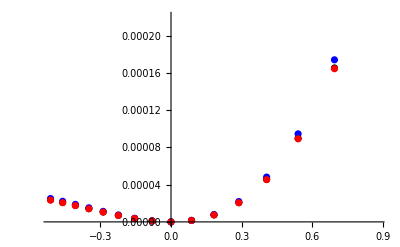

```mathematica
ListPlot[{{#1,Around[#2,#3]}&@@@vec25,{#1,Around[#2,#3]}&@@@vec20,{#1,Around[#2,#3]}&@@@vec30},PlotStyle->{Black,Blue,Red}]
```

### sigmazk

```mathematica
Nmax=25;Nx[Nmax_][i_]:=Floor[(i-1)/(Nmax+1)];Ny[Nmax_][i_]:=Mod[i-1,Nmax+1];
{k1,km1,k2,km2,k3,km3}={1,2,3,3,2,5};{A,B}={5,15};V=2;vec={};
```

```mathematica
vec={};AbsoluteTiming[Do[
ruleyp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[k2 B],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruleym=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[km2 Ny[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[k1 A],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexm=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[km1 Nx[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulex=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[km3(Nx[Nmax][j](Nx[Nmax][j]-1)(Nx[Nmax][j]-2))/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruley=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[k3(Nx[Nmax][j](Nx[Nmax][j]-1)Ny[Nmax][j])/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
Rsp1=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley]];
TRsp=Total[Rsp1];
ruleesc=Table[{i,i}->-TRsp[[i]],{i,(Nmax+1)^2}];
Rsp=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley,ruleesc]];
pss=SteadyState[Rsp];
ℒ=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j])∨(Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j])∨(Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]+1)∨(Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]-1)∨(Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]-1)∨(Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]+1),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
Ssp=Rsp;
(Ssp[[#2,#1]]=0)&@@@ℒ;
invS=Inverse[Ssp];
etS=MatrixExp[t Ssp];
Δμ=Log[(B k2 km1 k3)/(A km2 k1 km3)]//N;
set={#1,#2,Rsp[[#2,#1]]}&@@@ℒ;
ℒpA=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
ℒmA=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
ℒpB=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]+1),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
ℒmB=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]-1),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
setpA={#2,#1,Rsp[[#1,#2]]}&@@@ℒpA;setmA={#2,#1,Rsp[[#1,#2]]}&@@@ℒmA;
setpB={#2,#1,Rsp[[#1,#2]]}&@@@ℒpB;setmB={#2,#1,Rsp[[#1,#2]]}&@@@ℒmB;
sum={};errs={};
PLpA=PL[Rsp,etS,invS,pss,Kfun[set,pss]][setpA];
PLmA=PL[Rsp,etS,invS,pss,Kfun[set,pss]][setmA];
PLpB=PL[Rsp,etS,invS,pss,Kfun[set,pss]][setpB];
PLmB=PL[Rsp,etS,invS,pss,Kfun[set,pss]][setmB];
σzk=Kfun[set,pss]((PLpA-PLmA)Log[PLpA/PLmA]+(PLpB-PLmB)Log[PLpB/PLmB]);

ℒpC=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]-1),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
ℒmC=Flatten[Table[If[(Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]+1),{i,j},##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}],1];
setpC={#2,#1,Rsp[[#1,#2]]}&@@@ℒpC;setmC={#2,#1,Rsp[[#1,#2]]}&@@@ℒmC;
revset[setpA]=setmA;revset[setmA]=setpA;
revset[setpB]=setmB;revset[setmB]=setpB;
revset[setpC]=setmC;revset[setmC]=setpC;
seq={setpB,setpC,setmA};
seqr=Reverse[revset[#]&/@seq];
a=PLLL[Rsp,etS,invS,pss,Kfun[set,pss]][seq[[1]],seq[[2]],seq[[3]]];
b=PLLL[Rsp,etS,invS,pss,Kfun[set,pss]][seqr[[1]],seqr[[2]],seqr[[3]]];
A1=Log[a/b];
(*seq=RotateLeft[seq];
seqr=Reverse[revset[#]&/@seq];
a=PLL[Rsp,etS,invS,pss,Kfun[set,pss]][seq[[1]],seq[[2]]]PLGL[Rsp,etS,invS,pss,Kfun[set,pss]][seq[[2]],seq[[3]]];
b=PLL[Rsp,etS,invS,pss,Kfun[set,pss]][seqr[[1]],seqr[[2]]]PLGL[Rsp,etS,invS,pss,Kfun[set,pss]][seqr[[2]],seqr[[3]]];
A2=Log[a/b];
seq=RotateLeft[seq];
seqr=Reverse[revset[#]&/@seq];
a=PLL[Rsp,etS,invS,pss,Kfun[set,pss]][seq[[1]],seq[[2]]]PLGL[Rsp,etS,invS,pss,Kfun[set,pss]][seq[[2]],seq[[3]]];
b=PLL[Rsp,etS,invS,pss,Kfun[set,pss]][seqr[[1]],seqr[[2]]]PLGL[Rsp,etS,invS,pss,Kfun[set,pss]][seqr[[2]],seqr[[3]]];
A3=Log[a/b];*);

σti1=Kfun[set,pss](PLpB-PLmB)A1;
(*σti2=Kfun[set,pss](PLpB-PLmB)A2;
σti3=Kfun[set,pss](PLpB-PLmB)A3;*);

AppendTo[vec,{Δμ,σzk,σti1,EPR[Rsp](*,σti2,σti3*)}];
,{A,5,20}]][[1]]/60
vec
```

119.805

{{0.875469,3.34194,3.92558,3.92558},{0.693147,2.39721,2.76052,2.76052},{0.538997,1.61508,1.83341,1.83341},{0.405465,1.00057,1.12347,1.12347},{0.287682,0.54459,0.606165,0.606165},{0.182322,0.234308,0.258932,0.258932},{0.0870114,0.0567547,0.0623394,0.0623394},{0.,3.15877×10^-29,0.,-6.15059×10^-14},{-0.0800427,0.0534466,0.0581316,0.0581316},{-0.154151,0.207797,0.225094,0.225094},{-0.223144,0.454916,0.490988,0.490988},{-0.287682,0.787665,0.847321,0.847321},{-0.348307,1.19975,1.28675,1.28675},{-0.405465,1.6856,1.80287,1.80287},{-0.459532,2.24023,2.39004,2.39004},{-0.510826,2.85918,3.04326,3.04326}}

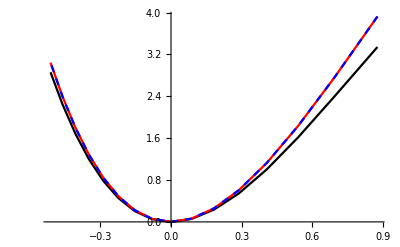

```mathematica
ListLinePlot[{{#1,#2}&@@@vec,{#1,#3}&@@@vec,{#1,#4}&@@@vec},PlotStyle->{Black,Red,{Blue,Dashed}}]
```

## counter example

```mathematica
R12=1;R21=7;R23=1;R32=2;
R34=5;R43=2;R41=1;R14=x;
```

```mathematica
vec={};Do[
R14=x;
R=({{0, R12, 0, x}, {R21, 0, R23, 0}, {0, R32, 0, R34}, {R41, 0, R43, 0}});
R-=DiagonalMatrix[Total[R]];
pss=SteadyState[R];σ=EPR[R];
edges=Table[{{i,Mod[i,4]+1},{Mod[i,4]+1,i}},{i,4}];
Z=Total[pss[[#1]]R[[#2,#1]]&@@@Flatten[edges,1]];
S=R;(S[[#2,#1]]=0)&@@@Flatten[edges,1];
etS=MatrixExp[t S];invS=Inverse[S];
L1p={{1,2,R21}};L1m={{2,1,R12}};
L2p={{2,3,R32}};L2m={{3,2,R23}};
L3p={{3,4,R43},{4,1,R14}};L3m={{4,3,R34},{1,4,R41}};
L3p2={{3,4,R43}};L3m2={{4,3,R34}};
L4p2={{4,1,R14}};L4m2={{1,4,R41}};
Lspace=Join[L1p,L1m,L2p,L2m,L3p,L3m];
allL={L1p,L1m,L2p,L2m,L3p,L3m};
allL2={L1p,L1m,L2p,L2m,L3p2,L3m2,L4p2,L4m2};
revv[L1p]=L1m;revv[L1m]=L1p;
revv[L2p]=L2m;revv[L2m]=L2p;
revv[L3p]=L3m;revv[L3m]=L3p;
revv[L3p2]=L3m2;revv[L3m2]=L3p2;
revv[L4p2]=L4m2;revv[L4m2]=L4p2;

σxℓcounter=0;Do[
σxℓcounter+=Z PLL[R,etS,invS,pss,Z][L1,L2]SmartLog[PLGL[R,etS,invS,pss,Z][L1,L2],PLGL[R,etS,invS,pss,Z][revv[L2],revv[L1]]];
,{L1,allL},{L2,allL}];
σxℓcounter2=0;Do[
σxℓcounter2+=Z PLL[R,etS,invS,pss,Z][L1,L2]SmartLog[PLGL[R,etS,invS,pss,Z][L1,L2],PLGL[R,etS,invS,pss,Z][revv[L2],revv[L1]]];
,{L1,allL2},{L2,allL2}];
remainders=0;
Do[
remainders+= Z PL[R,etS,invS,pss,Z][L]SmartLog[PL[R,etS,invS,pss,Z][L],PL[R,etS,invS,pss,Z][revv[L]]];
,{L,allL}];
Do[
remainders-=Z PL[R,etS,invS,pss,Z][L]SmartLog[PL[R,etS,invS,pss,Z][L],PL[R,etS,invS,pss,Z][revv[L]]];
,{L,allL2}];

AppendTo[vec,N@{x,σ,σxℓcounter,σxℓcounter2,remainders}]

,{x,.01,1,.05}]
```

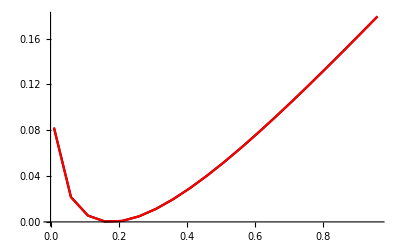

```mathematica
ListLinePlot[{{#1,#2}&@@@vec,{#1,#3+#5}&@@@vec},PlotStyle->{Black,Red}]
```

```mathematica
mark=#1&@@@Graphics`PlotMarkers[];
leg=Column[{LineLegend[{Black},{MaTeX["\\sigma",FontSize->15]}],LineLegend[{magentaviva},{MaTeX["\\sigma_{x,\\ell}",FontSize->15]}]},Automatic,-.3];
Show[
ListLinePlot[{#1,#2}&@@@vec,PlotStyle->Black,PlotRange->All],
ListLinePlot[{#1,#3}&@@@vec,PlotStyle->{magentaviva}],
Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["R_{14}",FontSize->15],""},Epilog->{Inset[leg,Scaled[{.84,.25}]]},ImageSize->250,AspectRatio->0.8,LabelStyle->{Black,FontFamily->"Times"},Axes->False]
```

-Graphics-

```mathematica
ΨAB=etS[[2,2]]R[[3,2]]
ΨBtAt=etS[[2,2]]R[[1,2]]
ΨBC=etS[[2,2]]R[[3,2]]
```

2. ⅇ^(-3. t)

1. ⅇ^(-3. t)

2. ⅇ^(-3. t)

```mathematica
ΨAB=etS[[L2p[[1,1]],L1p[[1,2]]]]L2p[[1,3]];
ΨBtAt=etS[[L1m[[1,1]],L2m[[1,2]]]]L1m[[1,3]];
ΨBC=etS[[L3p[[1,1]],L2p[[1,2]]]]L3p[[1,3]];
ΨCtBt=((pss[[#1]]#3&@@@L3m)[[1]])/Total[pss[[#1]]#3&@@@L3m] etS[[L2m[[1,1]],L3m[[1,2]]]]L2m[[1,3]];
ΨCA=((pss[[#1]]#3&@@@L3p)[[2]])/Total[pss[[#1]]#3&@@@L3p] etS[[L1p[[1,1]],L3p[[2,2]]]]L1p[[1,3]];
ΨAtCt=etS[[L3m[[2,1]],L1m[[1,2]]]]L3m[[2,3]];
ΨCC=((pss[[#1]]#3&@@@L3p)[[1]])/Total[pss[[#1]]#3&@@@L3p] etS[[L3p[[2,1]],L3p[[1,2]]]]L3p[[2,3]];
ΨCtCt=((pss[[#1]]#3&@@@L3m)[[2]])/Total[pss[[#1]]#3&@@@L3m] etS[[L3m[[1,1]],L3m[[2,2]]]]L3m[[1,3]];
```

```mathematica
Total[pss[[#1]]#3&@@@L1p]NIntegrate[ΨAB Log[ΨAB/ΨBtAt],{t,0,∞}]+Total[pss[[#1]]#3&@@@L2p]NIntegrate[ΨBC Log[ΨBC/ΨCtBt],{t,0,∞}]+Total[pss[[#1]]#3&@@@L3p]NIntegrate[ΨBC Log[ΨCA/ΨAtCt],{t,0,∞}]+Total[pss[[#1]]#3&@@@L3p]NIntegrate[ΨCC Log[ΨCC/ΨCtCt],{t,0,∞}]
```

0.644282

```mathematica
σ
```

0.179237

## Ben’s paper

### his plot

```mathematica
vec={};AbsoluteTiming[Do[
{R12,R21,R23,R32,R34,R43,R45,R54,R51,R15}=RandomReal[{0,6},10];
R=({{0, R12, 0, 0, R15}, {R21, 0, R23, 0, 0}, {0, R32, 0, R34, 0}, {0, 0, R43, 0, R45}, {R51, 0, 0, R54, 0}});
R-=DiagonalMatrix[Total[R]];
pss=SteadyState[R];σ=EPR[R];
II={{1,2,R21},{4,5,R54}};
JJ={{2,1,R12},{5,4,R45}};
rev[II]=JJ;rev[JJ]=II;
S=R;(S[[#2,#1]]=0)&@@@({#1,#2}&@@@Join[II,JJ]);
etS=MatrixExp[t S]//N;
σBT=0;σTC=0;
Do[
πI1=Total[pss[[#1]]#3&@@@I1];
πI2r=Total[pss[[#1]]#3&@@@rev[I2]];
Ψ=Sum[(pss[[i[[1]]]]i[[3]])/πI1 etS[[j[[1]],i[[2]]]]j[[3]],{i,I1},{j,I2}];
Ψr=Sum[(pss[[i[[1]]]]i[[3]])/πI2r etS[[j[[1]],i[[2]]]]j[[3]],{i,rev[I2]},{j,rev[I1]}];
σBT+=Quiet@NIntegrate[πI1 Ψ SmartLog[Ψ,Ψr],{t,0,∞}];
σTC+=πI1 Quiet@NIntegrate[Ψ,{t,0,∞}]SmartLog[πI1,πI2r];
,{I1,{II,JJ}},{I2,{II,JJ}}];
Q=(σBT+σTC)/(2σ);
A=SmartLog[R21 R32 R43 R54 R15,R12 R23 R34 R45 R51];
AppendTo[vec,Chop@N@{A,Q}]
,{rep,300}]][[1]]/60
```

NIntegrate::inumri: The integrand 0.689555 (0.+1.09329 (0.-0.761841 (0.+0.865327 Power[«2»])-0.832063 (0.-0.792297 Power[«2»]))+2.48535 (0.-0.0286234 (0.-1.04456 Power[«2»])+0.967747 (0.-0.0428053 Power[«2»])+0.0249047 (0.+0.462803 Power[«2»]))) If[0.+1.09329 (0.+Times[«2»]+Times[«2»])+2.48535 (0.+Times[«2»]+Times[«2»]+Times[«2»])≠0&&0.+1.96953 (0.+Times[«2»]+Times[«2»])+0.851478 (0.+Times[«2»]+Times[«2»]+Times[«2»])≠0,Log[(0.+1.09329 (0.+Times[«2»]+Times[«2»])+2.48535 (0.+Times[«2»]+Times[«2»]+Times[«2»]))/(0.+1.96953 Plus[«3»]+0.851478 Plus[«4»])],0] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,Root[{2297679721109433603602158447822035040391644609816087712561574296921665767739740233811096523+913220678840616840247330367310792756353073033255960090015884302827252618788123310213617463/10 Power[«2»]-1641072527053713363243048652819086305305857384737172984441558353674898391556984438479713538/5 Power[«2»]+236892437526680968733195136802138452643147058818378611230780922749394654855977378276171748 Power[«2»]-2297679721109433591032098247011156085522476001537567400849878473929343134916415773936918680 Power[«2»]&,3.651601932141075×10^-19}]}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

20.4556

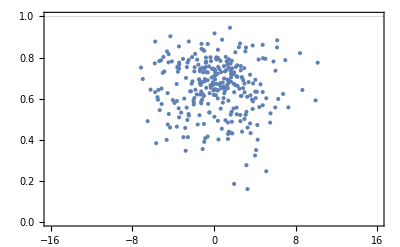

{-7.14594,10.1443}

{0.159817,151.648}

```mathematica
ListPlot[vec,Frame->True,GridLines->{{},{1}},PlotRange->{{-16,16},{0,1}}]
MinMax[#1&@@@vec]
MinMax[#2&@@@vec]
```

### my counterexample

```mathematica
vec2={};vec3={};Do[
R12=1;R21=7;R23=1;R32=2;
R34=5;R43=2;R41=1;R14=x;
R=({{0, R12, 0, R14}, {R21, 0, R23, 0}, {0, R32, 0, R34}, {R41, 0, R43, 0}});
R-=DiagonalMatrix[Total[R]];
pss=SteadyState[R];σ=EPR[R];
A={1,2,R21};Ar={2,1,R12};
B={2,3,R32};Br={3,2,R23};
CC={{3,4,R43},{4,1,R14}};CCr={{4,3,R34},{1,4,R41}};
rev[A]=Ar;rev[Ar]=A;
rev[B]=Br;rev[Br]=B;
rev[CC]=CCr;rev[CCr]=CC;
S=R;(S[[#2,#1]]=0)&@@@({#1,#2}&@@@Join[{A},{Ar},{B},{Br},CC,CCr]);
etS=MatrixExp[t S]//N;
σBT=0;σTC=0;
Do[
πI1=Total[pss[[#1]]#3&@@@I1];
πI2r=Total[pss[[#1]]#3&@@@rev[I2]];
Ψ=Sum[(pss[[i[[1]]]]i[[3]])/πI1 etS[[j[[1]],i[[2]]]]j[[3]],{i,I1},{j,I2}];
Ψr=Sum[(pss[[i[[1]]]]i[[3]])/πI2r etS[[j[[1]],i[[2]]]]j[[3]],{i,rev[I2]},{j,rev[I1]}];
σBT+=Quiet@NIntegrate[πI1 Ψ SmartLog[Ψ,Ψr],{t,0,∞}];
σTC+=πI1 Quiet@NIntegrate[Ψ,{t,0,∞}]SmartLog[πI1,πI2r];
,{I1,{{A},{Ar},{B},{Br},CC,CCr}},{I2,{{A},{Ar},{B},{Br},CC,CCr}}];
Q=(σBT+σTC)/(2σ);
Aff=SmartLog[R21 R32 R43 R14,R12 R23 R34 R41];
AppendTo[vec2,Chop@N@{x,Q}];
AppendTo[vec3,Chop@N@{x,(σBT+σTC)/2}];
,{x,0.1,1,.05}]
```

Part::partw: Part 7 of {0.0336879,0.248818,0.510638,0.206856} does not exist.

Part::partw: Part 7 of {{2.71828^(-8. t),0.,0.,0.},{0.,2.71828^(-3. t),0.,0.},{0.,0.,2.71828^(-3. t),0.},{0.,0.,0.,2.71828^(-5.1 t)}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NIntegrate::inumr: The integrand 0.235816 2.71828^(-3. t) If[1. 2.71828^(-3. t)≠0&&1. {{«4»},{«4»},{«4»},{«4»}}⟦7,1⟧≠0,Log[(1. 2.71828^(-3. t))/(1. {«4»}⟦7,1⟧)],0] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

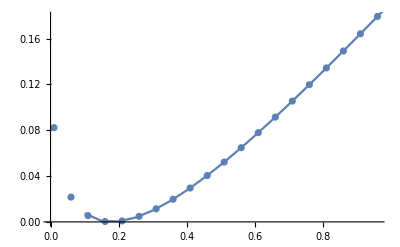

```mathematica
Show[ListPlot[{#1,#2}&@@@vec],ListLinePlot[vec3]]
```

```mathematica
K=Total[pss[[#1]]#3&@@@(Join[{A},{Ar},{B},{Br},CC,CCr])];
{KA,KAr,KB,KBr,KCC,KCCr}=Total[(pss[[#1]]#3&@@@#)]&/@{{A},{Ar},{B},{Br},CC,CCr};
a=(KA-KAr)/K Log[KA/KAr]+(KB-KBr)/K Log[KB/KBr]+(KCC-KCCr)/K Log[KCC/KCCr];
b=(KA-KAr)/K Log[KA/KAr]+(KB-KBr)/K Log[KB/KBr]+(KCC1-KCC1r)/K Log[KCC1/KCC1r]+(KCC2-KCC2r)/K Log[KCC2/KCC2r];
a-b
```

-0.0220655

### comparing expressions

```mathematica
R12=1;R21=7;R23=1;R32=2;
R34=5;R43=2;R41=1;R14=11;
R=({{0, R12, 0, R14}, {R21, 0, R23, 0}, {0, R32, 0, R34}, {R41, 0, R43, 0}});
R-=DiagonalMatrix[Total[R]];
pss=SteadyState[R];σ=EPR[R];
A={1,2,R21};Ar={2,1,R12};
B={2,3,R32};Br={3,2,R23};
CC={{3,4,R43},{4,1,R14}};CCr={{4,3,R34},{1,4,R41}};
rev[{A}]={Ar};rev[{Ar}]={A};
rev[{B}]={Br};rev[{Br}]={B};
rev[CC]=CCr;rev[CCr]=CC;
S=R;(S[[#2,#1]]=0)&@@@({#1,#2}&@@@Join[{A},{Ar},{B},{Br},CC,CCr]);
Z=Total[pss[[#1]]R[[#2,#1]]&@@@({#1,#2}&@@@Join[{A},{Ar},{B},{Br},CC,CCr])];
etS=MatrixExp[t S]//N;
invS=Inverse[S];
σBT=0;σTC=0;
Do[
πI1=Total[pss[[#1]]#3&@@@I1];
Ψ=Sum[(pss[[i[[1]]]]i[[3]])/πI1 etS[[j[[1]],i[[2]]]]j[[3]],{i,I1},{j,I2}];
Print[Simplify[πI1 Ψ-Z PtLL[R,etS,invS,pss,Z][t,I1,I2]]];
,{I1,{{A},{Ar},{B},{Br},CC,CCr}},{I2,{{A},{Ar},{B},{Br},CC,CCr}}];
```

0.

0

0

0.

0.

0.

0

0.

0.

0.

«1 more identical outputs»

0

0.

0.

0.

0

0

0.

0.

0

0

0.

0.

0.

0

0.

0.

0.

0

0

0.

0.

0.

0

0

0

## Gershgorin circles

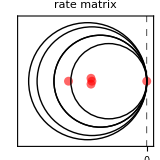
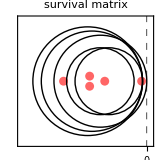

```mathematica
R={{0,1,2,3,4},{1,0,4,3,2},{5,4,0,3,2},{5,4,1,0,3},{3,4,2,2,0}}/10;
R=R-DiagonalMatrix[Total[R]];
S=R;(S[[#2,#1]]=0)&@@@{{1,2},{2,1},{3,4},{4,3}};
eigsR=Eigenvalues[R]//N;
eigsS=Eigenvalues[S]//N;
gcR=Table[{R[[i,i]],Total@Drop[R[[;;,i]],{i}]},{i,Length@R}];
gcS=Table[{S[[i,i]],Total@Drop[S[[;;,i]],{i}]},{i,Length@R}];

a=ListPlot[{Re[#],Im[#]}&/@eigsR,PlotStyle->{Red,PointSize->.04,Opacity[0.6]},Epilog->((Circle[{#1,0},#2])&@@@gcR),PlotRange->{{-3,.1},{-1.5,1.5}},ImageSize->160,LabelStyle->{Black,FontFamily->"Times New Roman"},PlotLabel->Style["rate matrix",FontFamily->"Times New Roman"],LabelStyle->Black,AspectRatio->1,Frame->True,FrameStyle->Black,GridLines->{{0},{}},GridLinesStyle->Directive[Dashed,Black],FrameLabel->{MaTeX["\\mathsf{Re}(\\lambda)",FontSize->12],MaTeX["\\mathsf{Im}(\\lambda)",FontSize->12]},FrameTicks->{None,{{0},None}}];
b=ListPlot[{Re[#],Im[#]}&/@eigsS,PlotStyle->{Red,PointSize->.04,Opacity[0.6]},Epilog->((Circle[{#1,0},#2])&@@@gcS),PlotRange->{{-3,.1},{-1.5,1.5}},ImageSize->160,LabelStyle->{Black,FontFamily->"Times New Roman"},PlotLabel->Style["survival matrix",FontFamily->"Times New Roman"],LabelStyle->Black,AspectRatio->1,Frame->True,FrameStyle->Black,GridLines->{{0},{}},GridLinesStyle->Directive[Dashed,Black],FrameLabel->{MaTeX["\\mathsf{Re}(\\lambda)",FontSize->12],MaTeX["\\mathsf{Im}(\\lambda)",FontSize->12]},FrameTicks->{None,{{0},None}}];
{a,b}
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["gershgorin_R.png",a,"PNG",ImageResolution->500]
Export["gershgorin_S.png",b,"PNG",ImageResolution->500]
```

gershgorin_R.png

gershgorin_S.png

-0.022204

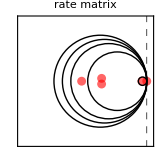
{-Graphics-,-Graphics-}

```mathematica
R={{0,1,2,3,0},{1,0,4,3,0},{5,4,0,3,0},{5,4,1,0,1},{0,0,0,1,0}}/10;
R=R-DiagonalMatrix[Total[R]];
S=R;(S[[#2,#1]]=0)&@@@{{5,4},{4,5}};
eigsR=Eigenvalues[R]//N;
eigsS=Eigenvalues[S]//N;
gcR=Table[{R[[i,i]],Total@Drop[R[[;;,i]],{i}]},{i,Length@R}];
gcS=Table[{S[[i,i]],Total@Drop[S[[;;,i]],{i}]},{i,Length@R}];
Max@Re@eigsS
a=ListPlot[{Re[#],Im[#]}&/@eigsR,PlotStyle->{Red,PointSize->.04,Opacity[0.6]},Epilog->((Circle[{#1,0},#2])&@@@gcR),PlotRange->{{-3,.1},{-1.5,1.5}},ImageSize->160,LabelStyle->{Black,FontFamily->"Times New Roman"},PlotLabel->Style["rate matrix",FontFamily->"Times New Roman"],LabelStyle->Black,AspectRatio->1,Frame->True,FrameStyle->Black,GridLines->{{0},{}},GridLinesStyle->Directive[Dashed,Black],FrameLabel->{MaTeX["\\mathsf{Re}(\\lambda)",FontSize->12],MaTeX["\\mathsf{Im}(\\lambda)",FontSize->12]},FrameTicks->None];
b=ListPlot[{Re[#],Im[#]}&/@eigsS,PlotStyle->{Red,PointSize->.04,Opacity[0.6]},Epilog->((Circle[{#1,0},#2])&@@@gcS),PlotRange->{{-3,.1},{-1.5,1.5}},ImageSize->160,LabelStyle->{Black,FontFamily->"Times New Roman"},PlotLabel->Style["survival matrix",FontFamily->"Times New Roman"],LabelStyle->Black,AspectRatio->1,Frame->True,FrameStyle->Black,GridLines->{{0},{}},GridLinesStyle->Directive[Dashed,Black],FrameLabel->{MaTeX["\\mathsf{Re}(\\lambda)",FontSize->12],MaTeX["\\mathsf{Im}(\\lambda)",FontSize->12]},FrameTicks->None];
{a,b}
```

```mathematica
DiagonalizableMatrixQ[S]
```

True